```mathematica
<<NumericalCalculus`
```

```mathematica
Λ[x_]=0.3127477*x-0.0231669*x^2-0.0005110 x^3-0.0000045 x^4;
```

20

2

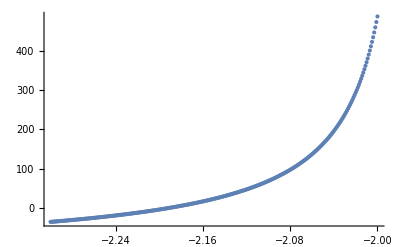

```mathematica
(*Shooting method to find the value for c for a particular value of 'Distance':We desire the solution to match the boundary condition that the derivative needs to be (c-Λ[c])/2, so we find the particular value of c where the solution to the differential equation will satisfy this condition.*)
(*Unfortuantely, the code is manual: it seems like there isn't a good way to determine the "minC" and "maxC" parameters and get good numerical results without inducing an extremely tiny step size that makes the program ridiculously slow.*)
R=20
Distance=2;
minC=-2.3;
maxC=-2;
list={};
list2={};
step=0.001;
Print[Distance];
For[c=minC,c≤maxC,c+=step,
sol=NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g[R]==0},g,{ξ,1.000001,R}];
temp[ξ_]=g[ξ]/.sol;
AppendTo[list, ND[temp[ξ],ξ,1.000001]-(c-Λ[c])/2];
AppendTo[list2, c];
];
xy=Thread @ {list2,Flatten[list]};
int=Interpolation[xy];
theC=x/.FindRoot[D[int[x]]==0,{x,minC}];
ListPlot[xy]
```

```mathematica
theC
```

-2.194

```mathematica
4*theC/Distance^2
```

-2.194

12

InterpolatingFunction[…][ξ]

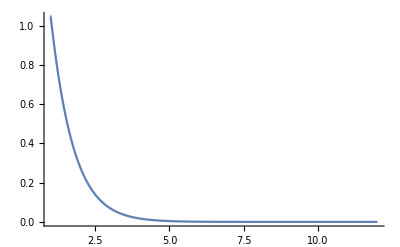

```mathematica
c=theC;
R=12
sol=First[NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g[R]==0},g,{ξ,1.000001,R}]];
r[ξ_]=g[ξ]/.sol
Plot[r[ξ]/.sol,{ξ,1.000001, R},PlotRange->All]
```

```mathematica
(*angular equation*)
c=theC;
phiSol=First[NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ[c]+c η^2)f[η]==0,f[0.999999999]==1,f[-0.999999999]==1},f,{η,-0.999999999,0.999999999}]]
```

{f→InterpolatingFunction[…]}

InterpolatingFunction[…][η]

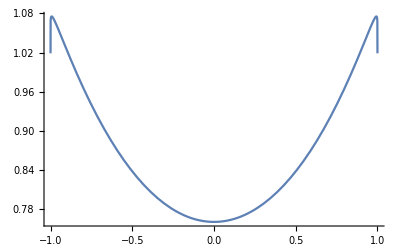

```mathematica
angSol[η_]=f[η]/.phiSol
Plot[angSol[η],{η,-1,1},PlotRange->All]
```

```mathematica
NIntegrate[angSol[η]^2,{η,-0.999999999,0.999999999}]
```

1.52158

```mathematica
NIntegrate[angSol[η]^2 r[ξ]^2 Distance^3/8(ξ^2-η^2),{ξ,1.000001,R},{η,-0.999999999,0.999999999}]
```

1.03242

```mathematica
ra[x_,z_]=√((z+Distance/2)^2+x^2);
rb[x_,z_]=√((z-Distance/2)^2+x^2);
ξ[x_,z_]=(ra[x,z]+rb[x,z])/Distance;
η[x_,z_]=(ra[x,z]-rb[x,z])/Distance;
ψ[ξ_,η_]=r[ξ]*angSol[η]
```

InterpolatingFunction[…][η] InterpolatingFunction[…][ξ]

```mathematica
Plot3D[ψ[ξ,η],{ξ,1.00001, R},{η,-0.999,0.999},PlotRange->All]
```

-Graphics3D-

```mathematica
ξ[0,0]
η[0,0]
```

1

0

```mathematica
ψ[1,0]
```

0.794609

```mathematica
Ψ1[x_,z_]=Piecewise[{{ψ[ξ[x,z],η[x,z]],x>0 && z>0},{ψ[ξ[-x,z],η[-x,z]],x<=0 && z>0},{ψ[ξ[x,-z],η[x,-z]],x>0&&z≤0},{ ψ[ξ[-x,-z],η[-x,-z]],x≤0&&z≤0}}];
```

```mathematica
Plot3D[Ψ1[x,z]^2,{x,-3,3},{z,-3,3},PlotRange->All]
```

-Graphics3D-

```mathematica
M=20;
theN=20;
minX=-3
maxX=3
minY=-3
maxY=3
electronDensity=Table[Ψ1[x,z]^2,{x,minX,maxX,(maxX-minX)/theN},{z,-5,5,(maxY-minY)/M}]*(1/NIntegrate[Ψ1[x,y]^2,{x,minX, maxX},{y,minY, maxY}])
Export[NotebookDirectory[]<>"electronDensity.csv",electronDensity]
```

-3

3

-3

3

/Users/Jessica/git/FiniteElementCode/electronDensity.csv

```mathematica
ListPlot3D[electronDensity,PlotRange->All]
```

-Graphics3D-

```mathematica
M=100;
theN=100;
minX=-5;
maxX=5;
minY=-5;
maxY=5;
electronDensity=N[Table[1/(√(2 π))^3 ⅇ^((-(x^2+y^2))/2),{x,minX,maxX,(maxX-minX)/theN},{y,minY,maxY,(maxY-minY)/M}]]
Export[NotebookDirectory[]<>"electronDensity.csv",electronDensity]
```

{{8.81796×10^-13,1.44658×10^-12,2.34951×10^-12,3.77804×10^-12,6.01469×10^-12,9.4802×10^-12,1.47938×10^-11,2.28558×10^-11,3.496×10^-11,5.29425×10^-11,7.93768×10^-11,1.17826×10^-10,1.73158×10^-10,2.51944×10^-10,3.62928×10^-10,5.17601×10^-10,7.30848×10^-10,1.02168×10^-9,1.41404×10^-9,1.9376×10^-9,2.6286×10^-9,3.53054×10^-9,4.69478×10^-9,6.18082×10^-9,8.05627×10^-9,1.03963×10^-8,1.32825×10^-8,1.68012×10^-8,2.10405×10^-8,2.60873×10^-8,3.20229×10^-8,3.89177×10^-8,4.68265×10^-8,5.57819×10^-8,6.57888×10^-8,7.68189×10^-8,8.88056×10^-8,1.01641×10^-7,1.15175×10^-7,1.29211×10^-7,1.43517×10^-7,1.57819×10^-7,1.7182×10^-7,1.85203×10^-7,1.97641×10^-7,2.08815×10^-7,2.18427×10^-7,2.26207×10^-7,2.31933×10^-7,2.35439×10^-7,2.36619×10^-7,2.35439×10^-7,2.31933×10^-7,2.26207×10^-7,2.18427×10^-7,2.08815×10^-7,1.97641×10^-7,1.85203×10^-7,1.7182×10^-7,1.57819×10^-7,1.43517×10^-7,1.29211×10^-7,1.15175×10^-7,1.01641×10^-7,8.88056×10^-8,7.68189×10^-8,6.57888×10^-8,5.57819×10^-8,4.68265×10^-8,3.89177×10^-8,3.20229×10^-8,2.60873×10^-8,2.10405×10^-8,1.68012×10^-8,1.32825×10^-8,1.03963×10^-8,8.05627×10^-9,6.18082×10^-9,4.69478×10^-9,3.53054×10^-9,2.6286×10^-9,1.9376×10^-9,1.41404×10^-9,1.02168×10^-9,7.30848×10^-10,5.17601×10^-10,3.62928×10^-10,2.51944×10^-10,1.73158×10^-10,1.17826×10^-10,7.93768×10^-11,5.29425×10^-11,3.496×10^-11,2.28558×10^-11,1.47938×10^-11,9.4802×10^-12,6.01469×10^-12,3.77804×10^-12,2.34951×10^-12,1.44658×10^-12,8.81796×10^-13},{1.44658×10^-12,2.37312×10^-12,3.85436×10^-12,6.19787×10^-12,9.8671×10^-12,1.55523×10^-11,2.42691×10^-11,3.74949×10^-11,5.73519×10^-11,8.6852×10^-11,1.30217×10^-10,1.93293×10^-10,2.84066×10^-10,4.13313×10^-10,5.95383×10^-10,8.49124×10^-10,1.19895×10^-9,1.67607×10^-9,2.31973×10^-9,3.17863×10^-9,4.31221×10^-9,5.79184×10^-9,7.70177×10^-9,1.01396×10^-8,1.32163×10^-8,1.70551×10^-8,2.179×10^-8,2.75623×10^-8,3.45169×10^-8,4.27962×10^-8,5.25335×10^-8,6.38445×10^-8,7.68189×10^-8,9.15102×10^-8,1.07926×10^-7,1.26021×10^-7,1.45686×10^-7,1.66742×10^-7,1.88944×10^-7,2.11971×10^-7,2.35439×10^-7,2.58902×10^-7,2.81871×10^-7,3.03825×10^-7,3.24229×10^-7,3.42561×10^-7,3.58329×10^-7,3.71092×10^-7,3.80486×10^-7,3.86237×10^-7,3.88173×10^-7,3.86237×10^-7,3.80486×10^-7,3.71092×10^-7,3.58329×10^-7,3.42561×10^-7,3.24229×10^-7,3.03825×10^-7,2.81871×10^-7,2.58902×10^-7,2.35439×10^-7,2.11971×10^-7,1.88944×10^-7,1.66742×10^-7,1.45686×10^-7,1.26021×10^-7,1.07926×10^-7,9.15102×10^-8,7.68189×10^-8,6.38445×10^-8,5.25335×10^-8,4.27962×10^-8,3.45169×10^-8,2.75623×10^-8,2.179×10^-8,1.70551×10^-8,1.32163×10^-8,1.01396×10^-8,7.70177×10^-9,5.79184×10^-9,4.31221×10^-9,3.17863×10^-9,2.31973×10^-9,1.67607×10^-9,1.19895×10^-9,8.49124×10^-10,5.95383×10^-10,4.13313×10^-10,2.84066×10^-10,1.93293×10^-10,1.30217×10^-10,8.6852×10^-11,5.73519×10^-11,3.74949×10^-11,2.42691×10^-11,1.55523×10^-11,9.8671×10^-12,6.19787×10^-12,3.85436×10^-12,2.37312×10^-12,1.44658×10^-12},{2.34951×10^-12,3.85436×10^-12,6.26016×10^-12,1.00664×10^-11,1.60259×10^-11,2.52596×10^-11,3.94173×10^-11,6.08983×10^-11,9.31495×10^-11,1.41063×10^-10,2.11496×10^-10,3.13941×10^-10,4.61372×10^-10,6.71293×10^-10,9.67007×10^-10,1.37913×10^-9,1.94731×10^-9,2.72223×10^-9,3.76765×10^-9,5.16265×10^-9,7.00378×10^-9,9.40696×10^-9,1.2509×10^-8,1.64685×10^-8,2.14656×10^-8,2.77005×10^-8,3.53907×10^-8,4.47661×10^-8,5.60616×10^-8,6.95086×10^-8,8.53235×10^-8,1.03695×10^-7,1.24767×10^-7,1.48629×10^-7,1.75291×10^-7,2.04681×10^-7,2.36619×10^-7,2.70819×10^-7,3.06878×10^-7,3.44278×10^-7,3.82394×10^-7,4.20502×10^-7,4.57808×10^-7,4.93464×10^-7,5.26605×10^-7,5.56379×10^-7,5.81988×10^-7,6.02718×10^-7,6.17976×10^-7,6.27316×10^-7,6.3046×10^-7,6.27316×10^-7,6.17976×10^-7,6.02718×10^-7,5.81988×10^-7,5.56379×10^-7,5.26605×10^-7,4.93464×10^-7,4.57808×10^-7,4.20502×10^-7,3.82394×10^-7,3.44278×10^-7,3.06878×10^-7,2.70819×10^-7,2.36619×10^-7,2.04681×10^-7,1.75291×10^-7,1.48629×10^-7,1.24767×10^-7,1.03695×10^-7,8.53235×10^-8,6.95086×10^-8,5.60616×10^-8,4.47661×10^-8,3.53907×10^-8,2.77005×10^-8,2.14656×10^-8,1.64685×10^-8,1.2509×10^-8,9.40696×10^-9,7.00378×10^-9,5.16265×10^-9,3.76765×10^-9,2.72223×10^-9,1.94731×10^-9,1.37913×10^-9,9.67007×10^-10,6.71293×10^-10,4.61372×10^-10,3.13941×10^-10,2.11496×10^-10,1.41063×10^-10,9.31495×10^-11,6.08983×10^-11,3.94173×10^-11,2.52596×10^-11,1.60259×10^-11,1.00664×10^-11,6.26016×10^-12,3.85436×10^-12,2.34951×10^-12},{3.77804×10^-12,6.19787×10^-12,1.00664×10^-11,1.6187×10^-11,2.57699×10^-11,4.06178×10^-11,6.33836×10^-11,9.79254×10^-11,1.49786×10^-10,2.26831×10^-10,3.40088×10^-10,5.04822×10^-10,7.41893×10^-10,1.07945×10^-9,1.55496×10^-9,2.21765×10^-9,3.13131×10^-9,4.37738×10^-9,6.05843×10^-9,8.30162×10^-9,1.12622×10^-8,1.51265×10^-8,2.01147×10^-8,2.64816×10^-8,3.45169×10^-8,4.45428×10^-8,5.69088×10^-8,7.19845×10^-8,9.01478×10^-8,1.11771×10^-7,1.37201×10^-7,1.66742×10^-7,2.00628×10^-7,2.38997×10^-7,2.81871×10^-7,3.29129×10^-7,3.80486×10^-7,4.35481×10^-7,4.93464×10^-7,5.53604×10^-7,6.14894×10^-7,6.76174×10^-7,7.36162×10^-7,7.93497×10^-7,8.46788×10^-7,8.94666×10^-7,9.35845×10^-7,9.6918×10^-7,9.93715×10^-7,1.00873×10^-6,1.01379×10^-6,1.00873×10^-6,9.93715×10^-7,9.6918×10^-7,9.35845×10^-7,8.94666×10^-7,8.46788×10^-7,7.93497×10^-7,7.36162×10^-7,6.76174×10^-7,6.14894×10^-7,5.53604×10^-7,4.93464×10^-7,4.35481×10^-7,3.80486×10^-7,3.29129×10^-7,2.81871×10^-7,2.38997×10^-7,2.00628×10^-7,1.66742×10^-7,1.37201×10^-7,1.11771×10^-7,9.01478×10^-8,7.19845×10^-8,5.69088×10^-8,4.45428×10^-8,3.45169×10^-8,2.64816×10^-8,2.01147×10^-8,1.51265×10^-8,1.12622×10^-8,8.30162×10^-9,6.05843×10^-9,4.37738×10^-9,3.13131×10^-9,2.21765×10^-9,1.55496×10^-9,1.07945×10^-9,7.41893×10^-10,5.04822×10^-10,3.40088×10^-10,2.26831×10^-10,1.49786×10^-10,9.79254×10^-11,6.33836×10^-11,4.06178×10^-11,2.57699×10^-11,1.6187×10^-11,1.00664×10^-11,6.19787×10^-12,3.77804×10^-12},{6.01469×10^-12,9.8671×10^-12,1.60259×10^-11,2.57699×10^-11,4.1026×10^-11,6.46641×10^-11,1.00908×10^-10,1.55899×10^-10,2.38461×10^-10,3.61118×10^-10,5.41426×10^-10,8.03683×10^-10,1.1811×10^-9,1.7185×10^-9,2.47552×10^-9,3.53054×10^-9,4.98508×10^-9,6.96885×10^-9,9.6451×10^-9,1.32163×10^-8,1.79296×10^-8,2.40817×10^-8,3.20229×10^-8,4.21591×10^-8,5.49515×10^-8,7.09127×10^-8,9.05996×10^-8,1.146×10^-7,1.43517×10^-7,1.77941×10^-7,2.18427×10^-7,2.65456×10^-7,3.19402×10^-7,3.80486×10^-7,4.48743×10^-7,5.23978×10^-7,6.0574×10^-7,6.93291×10^-7,7.85602×10^-7,8.81346×10^-7,9.7892×10^-7,1.07648×10^-6,1.17198×10^-6,1.26326×10^-6,1.3481×10^-6,1.42432×10^-6,1.48988×10^-6,1.54295×10^-6,1.58201×10^-6,1.60592×10^-6,1.61397×10^-6,1.60592×10^-6,1.58201×10^-6,1.54295×10^-6,1.48988×10^-6,1.42432×10^-6,1.3481×10^-6,1.26326×10^-6,1.17198×10^-6,1.07648×10^-6,9.7892×10^-7,8.81346×10^-7,7.85602×10^-7,6.93291×10^-7,6.0574×10^-7,5.23978×10^-7,4.48743×10^-7,3.80486×10^-7,3.19402×10^-7,2.65456×10^-7,2.18427×10^-7,1.77941×10^-7,1.43517×10^-7,1.146×10^-7,9.05996×10^-8,7.09127×10^-8,5.49515×10^-8,4.21591×10^-8,3.20229×10^-8,2.40817×10^-8,1.79296×10^-8,1.32163×10^-8,9.6451×10^-9,6.96885×10^-9,4.98508×10^-9,3.53054×10^-9,2.47552×10^-9,1.7185×10^-9,1.1811×10^-9,8.03683×10^-10,5.41426×10^-10,3.61118×10^-10,2.38461×10^-10,1.55899×10^-10,1.00908×10^-10,6.46641×10^-11,4.1026×10^-11,2.57699×10^-11,1.60259×10^-11,9.8671×10^-12,6.01469×10^-12},{9.4802×10^-12,1.55523×10^-11,2.52596×10^-11,4.06178×10^-11,6.46641×10^-11,1.01922×10^-10,1.59048×10^-10,2.45723×10^-10,3.75856×10^-10,5.69185×10^-10,8.5338×10^-10,1.26674×10^-9,1.86163×10^-9,2.70865×10^-9,3.90185×10^-9,5.56474×10^-9,7.85736×10^-9,1.09841×10^-8,1.52024×10^-8,2.08312×10^-8,2.82601×10^-8,3.79569×10^-8,5.04736×10^-8,6.645×10^-8,8.6613×10^-8,1.11771×10^-7,1.42801×10^-7,1.8063×10^-7,2.26207×10^-7,2.80465×10^-7,3.44278×10^-7,4.18405×10^-7,5.03433×10^-7,5.99712×10^-7,7.07297×10^-7,8.25881×10^-7,9.54751×10^-7,1.09275×10^-6,1.23824×10^-6,1.38915×10^-6,1.54295×10^-6,1.69672×10^-6,1.84724×10^-6,1.99112×10^-6,2.12484×10^-6,2.24498×10^-6,2.34831×10^-6,2.43195×10^-6,2.49352×10^-6,2.5312×10^-6,2.54389×10^-6,2.5312×10^-6,2.49352×10^-6,2.43195×10^-6,2.34831×10^-6,2.24498×10^-6,2.12484×10^-6,1.99112×10^-6,1.84724×10^-6,1.69672×10^-6,1.54295×10^-6,1.38915×10^-6,1.23824×10^-6,1.09275×10^-6,9.54751×10^-7,8.25881×10^-7,7.07297×10^-7,5.99712×10^-7,5.03433×10^-7,4.18405×10^-7,3.44278×10^-7,2.80465×10^-7,2.26207×10^-7,1.8063×10^-7,1.42801×10^-7,1.11771×10^-7,8.6613×10^-8,6.645×10^-8,5.04736×10^-8,3.79569×10^-8,2.82601×10^-8,2.08312×10^-8,1.52024×10^-8,1.09841×10^-8,7.85736×10^-9,5.56474×10^-9,3.90185×10^-9,2.70865×10^-9,1.86163×10^-9,1.26674×10^-9,8.5338×10^-10,5.69185×10^-10,3.75856×10^-10,2.45723×10^-10,1.59048×10^-10,1.01922×10^-10,6.46641×10^-11,4.06178×10^-11,2.52596×10^-11,1.55523×10^-11,9.4802×10^-12},{1.47938×10^-11,2.42691×10^-11,3.94173×10^-11,6.33836×10^-11,1.00908×10^-10,1.59048×10^-10,2.48193×10^-10,3.83449×10^-10,5.86519×10^-10,8.88208×10^-10,1.33169×10^-9,1.97674×10^-9,2.90505×10^-9,4.22682×10^-9,6.0888×10^-9,8.68372×10^-9,1.22613×10^-8,1.71406×10^-8,2.37231×10^-8,3.25068×10^-8,4.40996×10^-8,5.92313×10^-8,7.87635×10^-8,1.03695×10^-7,1.35159×10^-7,1.74417×10^-7,2.22839×10^-7,2.81871×10^-7,3.52994×10^-7,4.37663×10^-7,5.37243×10^-7,6.52917×10^-7,7.85602×10^-7,9.35845×10^-7,1.10373×10^-6,1.28878×10^-6,1.48988×10^-6,1.70522×10^-6,1.93227×10^-6,2.16776×10^-6,2.40776×10^-6,2.64771×10^-6,2.88261×10^-6,3.10712×10^-6,3.31579×10^-6,3.50326×10^-6,3.66451×10^-6,3.79504×10^-6,3.89111×10^-6,3.94992×10^-6,3.96972×10^-6,3.94992×10^-6,3.89111×10^-6,3.79504×10^-6,3.66451×10^-6,3.50326×10^-6,3.31579×10^-6,3.10712×10^-6,2.88261×10^-6,2.64771×10^-6,2.40776×10^-6,2.16776×10^-6,1.93227×10^-6,1.70522×10^-6,1.48988×10^-6,1.28878×10^-6,1.10373×10^-6,9.35845×10^-7,7.85602×10^-7,6.52917×10^-7,5.37243×10^-7,4.37663×10^-7,3.52994×10^-7,2.81871×10^-7,2.22839×10^-7,1.74417×10^-7,1.35159×10^-7,1.03695×10^-7,7.87635×10^-8,5.92313×10^-8,4.40996×10^-8,3.25068×10^-8,2.37231×10^-8,1.71406×10^-8,1.22613×10^-8,8.68372×10^-9,6.0888×10^-9,4.22682×10^-9,2.90505×10^-9,1.97674×10^-9,1.33169×10^-9,8.88208×10^-10,5.86519×10^-10,3.83449×10^-10,2.48193×10^-10,1.59048×10^-10,1.00908×10^-10,6.33836×10^-11,3.94173×10^-11,2.42691×10^-11,1.47938×10^-11},{2.28558×10^-11,3.74949×10^-11,6.08983×10^-11,9.79254×10^-11,1.55899×10^-10,2.45723×10^-10,3.83449×10^-10,5.92414×10^-10,9.06151×10^-10,1.37225×10^-9,2.05741×10^-9,3.05399×10^-9,4.48819×10^-9,6.53028×10^-9,9.40696×10^-9,1.3416×10^-8,1.89433×10^-8,2.64816×10^-8,3.66513×10^-8,5.02219×10^-8,6.81322×10^-8,9.15102×10^-8,1.21687×10^-7,1.60204×10^-7,2.08815×10^-7,2.69468×10^-7,3.44278×10^-7,4.35481×10^-7,5.45362×10^-7,6.76174×10^-7,8.3002×10^-7,1.00873×10^-6,1.21373×10^-6,1.44585×10^-6,1.70522×10^-6,1.99112×10^-6,2.30181×10^-6,2.6345×10^-6,2.98528×10^-6,3.34911×10^-6,3.71989×10^-6,4.09061×10^-6,4.45352×10^-6,4.80038×10^-6,5.12277×10^-6,5.41241×10^-6,5.66153×10^-6,5.8632×10^-6,6.01162×10^-6,6.10248×10^-6,6.13307×10^-6,6.10248×10^-6,6.01162×10^-6,5.8632×10^-6,5.66153×10^-6,5.41241×10^-6,5.12277×10^-6,4.80038×10^-6,4.45352×10^-6,4.09061×10^-6,3.71989×10^-6,3.34911×10^-6,2.98528×10^-6,2.6345×10^-6,2.30181×10^-6,1.99112×10^-6,1.70522×10^-6,1.44585×10^-6,1.21373×10^-6,1.00873×10^-6,8.3002×10^-7,6.76174×10^-7,5.45362×10^-7,4.35481×10^-7,3.44278×10^-7,2.69468×10^-7,2.08815×10^-7,1.60204×10^-7,1.21687×10^-7,9.15102×10^-8,6.81322×10^-8,5.02219×10^-8,3.66513×10^-8,2.64816×10^-8,1.89433×10^-8,1.3416×10^-8,9.40696×10^-9,6.53028×10^-9,4.48819×10^-9,3.05399×10^-9,2.05741×10^-9,1.37225×10^-9,9.06151×10^-10,5.92414×10^-10,3.83449×10^-10,2.45723×10^-10,1.55899×10^-10,9.79254×10^-11,6.08983×10^-11,3.74949×10^-11,2.28558×10^-11},{3.496×10^-11,5.73519×10^-11,9.31495×10^-11,1.49786×10^-10,2.38461×10^-10,3.75856×10^-10,5.86519×10^-10,9.06151×10^-10,1.38604×10^-9,2.09898×10^-9,3.147×10^-9,4.67136×10^-9,6.8651×10^-9,9.98866×10^-9,1.43888×10^-8,2.0521×10^-8,2.89755×10^-8,4.0506×10^-8,5.60616×10^-8,7.68189×10^-8,1.04214×10^-7,1.39973×10^-7,1.86131×10^-7,2.45047×10^-7,3.19402×10^-7,4.12176×10^-7,5.26605×10^-7,6.66107×10^-7,8.34181×10^-7,1.03427×10^-6,1.26959×10^-6,1.54295×10^-6,1.8565×10^-6,2.21155×10^-6,2.60829×10^-6,3.04559×10^-6,3.52082×10^-6,4.02971×10^-6,4.56626×10^-6,5.12277×10^-6,5.68991×10^-6,6.25696×10^-6,6.81206×10^-6,7.34261×10^-6,7.83574×10^-6,8.27877×10^-6,8.65983×10^-6,8.96829×10^-6,9.19532×10^-6,9.33429×10^-6,9.38108×10^-6,9.33429×10^-6,9.19532×10^-6,8.96829×10^-6,8.65983×10^-6,8.27877×10^-6,7.83574×10^-6,7.34261×10^-6,6.81206×10^-6,6.25696×10^-6,5.68991×10^-6,5.12277×10^-6,4.56626×10^-6,4.02971×10^-6,3.52082×10^-6,3.04559×10^-6,2.60829×10^-6,2.21155×10^-6,1.8565×10^-6,1.54295×10^-6,1.26959×10^-6,1.03427×10^-6,8.34181×10^-7,6.66107×10^-7,5.26605×10^-7,4.12176×10^-7,3.19402×10^-7,2.45047×10^-7,1.86131×10^-7,1.39973×10^-7,1.04214×10^-7,7.68189×10^-8,5.60616×10^-8,4.0506×10^-8,2.89755×10^-8,2.0521×10^-8,1.43888×10^-8,9.98866×10^-9,6.8651×10^-9,4.67136×10^-9,3.147×10^-9,2.09898×10^-9,1.38604×10^-9,9.06151×10^-10,5.86519×10^-10,3.75856×10^-10,2.38461×10^-10,1.49786×10^-10,9.31495×10^-11,5.73519×10^-11,3.496×10^-11},{5.29425×10^-11,8.6852×10^-11,1.41063×10^-10,2.26831×10^-10,3.61118×10^-10,5.69185×10^-10,8.88208×10^-10,1.37225×10^-9,2.09898×10^-9,3.17863×10^-9,4.76573×10^-9,7.07417×10^-9,1.03963×10^-8,1.51265×10^-8,2.179×10^-8,3.10764×10^-8,4.38796×10^-8,6.13411×10^-8,8.4898×10^-8,1.16332×10^-7,1.57819×10^-7,2.11971×10^-7,2.81871×10^-7,3.71092×10^-7,4.83693×10^-7,6.24187×10^-7,7.97475×10^-7,1.00873×10^-6,1.26326×10^-6,1.56627×10^-6,1.92263×10^-6,2.3366×10^-6,2.81143×10^-6,3.34911×10^-6,3.94992×10^-6,4.61215×10^-6,5.33183×10^-6,6.10248×10^-6,6.91501×10^-6,7.75777×10^-6,8.61664×10^-6,9.47536×10^-6,0.000010316,0.0000111194,0.0000118662,0.0000125371,0.0000131142,0.0000135813,0.0000139251,0.0000141356,0.0000142064,0.0000141356,0.0000139251,0.0000135813,0.0000131142,0.0000125371,0.0000118662,0.0000111194,0.000010316,9.47536×10^-6,8.61664×10^-6,7.75777×10^-6,6.91501×10^-6,6.10248×10^-6,5.33183×10^-6,4.61215×10^-6,3.94992×10^-6,3.34911×10^-6,2.81143×10^-6,2.3366×10^-6,1.92263×10^-6,1.56627×10^-6,1.26326×10^-6,1.00873×10^-6,7.97475×10^-7,6.24187×10^-7,4.83693×10^-7,3.71092×10^-7,2.81871×10^-7,2.11971×10^-7,1.57819×10^-7,1.16332×10^-7,8.4898×10^-8,6.13411×10^-8,4.38796×10^-8,3.10764×10^-8,2.179×10^-8,1.51265×10^-8,1.03963×10^-8,7.07417×10^-9,4.76573×10^-9,3.17863×10^-9,2.09898×10^-9,1.37225×10^-9,8.88208×10^-10,5.69185×10^-10,3.61118×10^-10,2.26831×10^-10,1.41063×10^-10,8.6852×10^-11,5.29425×10^-11},{7.93768×10^-11,1.30217×10^-10,2.11496×10^-10,3.40088×10^-10,5.41426×10^-10,8.5338×10^-10,1.33169×10^-9,2.05741×10^-9,3.147×10^-9,4.76573×10^-9,7.14527×10^-9,1.06063×10^-8,1.55872×10^-8,2.26792×10^-8,3.26698×10^-8,4.6593×10^-8,6.57888×10^-8,9.19689×10^-8,1.27288×10^-7,1.74417×10^-7,2.36619×10^-7,3.17809×10^-7,4.2261×10^-7,5.56379×10^-7,7.25202×10^-7,9.35845×10^-7,1.19566×10^-6,1.5124×10^-6,1.89401×10^-6,2.34831×10^-6,2.88261×10^-6,3.50326×10^-6,4.21519×10^-6,5.02133×10^-6,5.92212×10^-6,6.91501×10^-6,7.99403×10^-6,9.14946×10^-6,0.0000103677,0.0000116312,0.0000129189,0.0000142064,0.0000154668,0.0000166714,0.000017791,0.000018797,0.0000196621,0.0000203625,0.000020878,0.0000211935,0.0000212997,0.0000211935,0.000020878,0.0000203625,0.0000196621,0.000018797,0.000017791,0.0000166714,0.0000154668,0.0000142064,0.0000129189,0.0000116312,0.0000103677,9.14946×10^-6,7.99403×10^-6,6.91501×10^-6,5.92212×10^-6,5.02133×10^-6,4.21519×10^-6,3.50326×10^-6,2.88261×10^-6,2.34831×10^-6,1.89401×10^-6,1.5124×10^-6,1.19566×10^-6,9.35845×10^-7,7.25202×10^-7,5.56379×10^-7,4.2261×10^-7,3.17809×10^-7,2.36619×10^-7,1.74417×10^-7,1.27288×10^-7,9.19689×10^-8,6.57888×10^-8,4.6593×10^-8,3.26698×10^-8,2.26792×10^-8,1.55872×10^-8,1.06063×10^-8,7.14527×10^-9,4.76573×10^-9,3.147×10^-9,2.05741×10^-9,1.33169×10^-9,8.5338×10^-10,5.41426×10^-10,3.40088×10^-10,2.11496×10^-10,1.30217×10^-10,7.93768×10^-11},{1.17826×10^-10,1.93293×10^-10,3.13941×10^-10,5.04822×10^-10,8.03683×10^-10,1.26674×10^-9,1.97674×10^-9,3.05399×10^-9,4.67136×10^-9,7.07417×10^-9,1.06063×10^-8,1.57439×10^-8,2.31374×10^-8,3.36647×10^-8,4.84945×10^-8,6.91619×10^-8,9.76559×10^-8,1.36517×10^-7,1.88944×10^-7,2.58902×10^-7,3.51233×10^-7,4.7175×10^-7,6.27316×10^-7,8.25881×10^-7,1.07648×10^-6,1.38915×10^-6,1.77481×10^-6,2.24498×10^-6,2.81143×10^-6,3.48579×10^-6,4.2789×10^-6,5.20019×10^-6,6.25696×10^-6,7.45358×10^-6,8.79071×10^-6,0.0000102645,0.0000118662,0.0000135813,0.0000153896,0.0000172652,0.0000191767,0.0000210878,0.0000229587,0.0000247468,0.0000264087,0.0000279019,0.0000291862,0.0000302258,0.0000309909,0.0000314593,0.000031617,0.0000314593,0.0000309909,0.0000302258,0.0000291862,0.0000279019,0.0000264087,0.0000247468,0.0000229587,0.0000210878,0.0000191767,0.0000172652,0.0000153896,0.0000135813,0.0000118662,0.0000102645,8.79071×10^-6,7.45358×10^-6,6.25696×10^-6,5.20019×10^-6,4.2789×10^-6,3.48579×10^-6,2.81143×10^-6,2.24498×10^-6,1.77481×10^-6,1.38915×10^-6,1.07648×10^-6,8.25881×10^-7,6.27316×10^-7,4.7175×10^-7,3.51233×10^-7,2.58902×10^-7,1.88944×10^-7,1.36517×10^-7,9.76559×10^-8,6.91619×10^-8,4.84945×10^-8,3.36647×10^-8,2.31374×10^-8,1.57439×10^-8,1.06063×10^-8,7.07417×10^-9,4.67136×10^-9,3.05399×10^-9,1.97674×10^-9,1.26674×10^-9,8.03683×10^-10,5.04822×10^-10,3.13941×10^-10,1.93293×10^-10,1.17826×10^-10},{1.73158×10^-10,2.84066×10^-10,4.61372×10^-10,7.41893×10^-10,1.1811×10^-9,1.86163×10^-9,2.90505×10^-9,4.48819×10^-9,6.8651×10^-9,1.03963×10^-8,1.55872×10^-8,2.31374×10^-8,3.40031×10^-8,4.94741×10^-8,7.12682×10^-8,1.01641×10^-7,1.43517×10^-7,2.00628×10^-7,2.77675×10^-7,3.80486×10^-7,5.16177×10^-7,6.93291×10^-7,9.21912×10^-7,1.21373×10^-6,1.58201×10^-6,2.04152×10^-6,2.60829×10^-6,3.29925×10^-6,4.13172×10^-6,5.12277×10^-6,6.28833×10^-6,7.64227×10^-6,9.19532×10^-6,0.0000109539,0.0000129189,0.0000150849,0.0000174388,0.0000199593,0.0000226168,0.0000253732,0.0000281823,0.0000309909,0.0000337404,0.0000363682,0.0000388107,0.000041005,0.0000428924,0.0000444202,0.0000455447,0.0000462331,0.0000464648,0.0000462331,0.0000455447,0.0000444202,0.0000428924,0.000041005,0.0000388107,0.0000363682,0.0000337404,0.0000309909,0.0000281823,0.0000253732,0.0000226168,0.0000199593,0.0000174388,0.0000150849,0.0000129189,0.0000109539,9.19532×10^-6,7.64227×10^-6,6.28833×10^-6,5.12277×10^-6,4.13172×10^-6,3.29925×10^-6,2.60829×10^-6,2.04152×10^-6,1.58201×10^-6,1.21373×10^-6,9.21912×10^-7,6.93291×10^-7,5.16177×10^-7,3.80486×10^-7,2.77675×10^-7,2.00628×10^-7,1.43517×10^-7,1.01641×10^-7,7.12682×10^-8,4.94741×10^-8,3.40031×10^-8,2.31374×10^-8,1.55872×10^-8,1.03963×10^-8,6.8651×10^-9,4.48819×10^-9,2.90505×10^-9,1.86163×10^-9,1.1811×10^-9,7.41893×10^-10,4.61372×10^-10,2.84066×10^-10,1.73158×10^-10},{2.51944×10^-10,4.13313×10^-10,6.71293×10^-10,1.07945×10^-9,1.7185×10^-9,2.70865×10^-9,4.22682×10^-9,6.53028×10^-9,9.98866×10^-9,1.51265×10^-8,2.26792×10^-8,3.36647×10^-8,4.94741×10^-8,7.19845×10^-8,1.03695×10^-7,1.47887×10^-7,2.08815×10^-7,2.91911×10^-7,4.04014×10^-7,5.53604×10^-7,7.51033×10^-7,1.00873×10^-6,1.34137×10^-6,1.76596×10^-6,2.30181×10^-6,2.9704×10^-6,3.79504×10^-6,4.80038×10^-6,6.01162×10^-6,7.45358×10^-6,9.14946×10^-6,0.0000111194,0.0000133791,0.0000159378,0.000018797,0.0000219484,0.0000253732,0.0000290406,0.0000329073,0.0000369178,0.000041005,0.0000450916,0.0000490919,0.0000529154,0.0000564692,0.000059662,0.0000624081,0.0000646311,0.0000662672,0.0000672687,0.0000676059,0.0000672687,0.0000662672,0.0000646311,0.0000624081,0.000059662,0.0000564692,0.0000529154,0.0000490919,0.0000450916,0.000041005,0.0000369178,0.0000329073,0.0000290406,0.0000253732,0.0000219484,0.000018797,0.0000159378,0.0000133791,0.0000111194,9.14946×10^-6,7.45358×10^-6,6.01162×10^-6,4.80038×10^-6,3.79504×10^-6,2.9704×10^-6,2.30181×10^-6,1.76596×10^-6,1.34137×10^-6,1.00873×10^-6,7.51033×10^-7,5.53604×10^-7,4.04014×10^-7,2.91911×10^-7,2.08815×10^-7,1.47887×10^-7,1.03695×10^-7,7.19845×10^-8,4.94741×10^-8,3.36647×10^-8,2.26792×10^-8,1.51265×10^-8,9.98866×10^-9,6.53028×10^-9,4.22682×10^-9,2.70865×10^-9,1.7185×10^-9,1.07945×10^-9,6.71293×10^-10,4.13313×10^-10,2.51944×10^-10},{3.62928×10^-10,5.95383×10^-10,9.67007×10^-10,1.55496×10^-9,2.47552×10^-9,3.90185×10^-9,6.0888×10^-9,9.40696×10^-9,1.43888×10^-8,2.179×10^-8,3.26698×10^-8,4.84945×10^-8,7.12682×10^-8,1.03695×10^-7,1.49374×10^-7,2.13034×10^-7,3.00801×10^-7,4.20502×10^-7,5.81988×10^-7,7.97475×10^-7,1.08187×10^-6,1.45309×10^-6,1.93227×10^-6,2.54389×10^-6,3.31579×10^-6,4.2789×10^-6,5.46681×10^-6,6.91501×10^-6,8.65983×10^-6,0.000010737,0.0000131799,0.0000160177,0.0000192728,0.0000229587,0.0000270773,0.000031617,0.0000365505,0.0000418334,0.0000474034,0.0000531807,0.0000590683,0.000064955,0.0000707176,0.0000762254,0.0000813446,0.0000859439,0.0000898997,0.0000931019,0.0000954588,0.0000969015,0.0000973872,0.0000969015,0.0000954588,0.0000931019,0.0000898997,0.0000859439,0.0000813446,0.0000762254,0.0000707176,0.000064955,0.0000590683,0.0000531807,0.0000474034,0.0000418334,0.0000365505,0.000031617,0.0000270773,0.0000229587,0.0000192728,0.0000160177,0.0000131799,0.000010737,8.65983×10^-6,6.91501×10^-6,5.46681×10^-6,4.2789×10^-6,3.31579×10^-6,2.54389×10^-6,1.93227×10^-6,1.45309×10^-6,1.08187×10^-6,7.97475×10^-7,5.81988×10^-7,4.20502×10^-7,3.00801×10^-7,2.13034×10^-7,1.49374×10^-7,1.03695×10^-7,7.12682×10^-8,4.84945×10^-8,3.26698×10^-8,2.179×10^-8,1.43888×10^-8,9.40696×10^-9,6.0888×10^-9,3.90185×10^-9,2.47552×10^-9,1.55496×10^-9,9.67007×10^-10,5.95383×10^-10,3.62928×10^-10},{5.17601×10^-10,8.49124×10^-10,1.37913×10^-9,2.21765×10^-9,3.53054×10^-9,5.56474×10^-9,8.68372×10^-9,1.3416×10^-8,2.0521×10^-8,3.10764×10^-8,4.6593×10^-8,6.91619×10^-8,1.01641×10^-7,1.47887×10^-7,2.13034×10^-7,3.03825×10^-7,4.28997×10^-7,5.99712×10^-7,8.3002×10^-7,1.13734×10^-6,1.54295×10^-6,2.07237×10^-6,2.75576×10^-6,3.62805×10^-6,4.72891×10^-6,6.10248×10^-6,7.79666×10^-6,9.86206×10^-6,0.0000123505,0.0000153129,0.000018797,0.0000228441,0.0000274865,0.0000327432,0.0000386171,0.0000450916,0.0000521276,0.000059662,0.0000676059,0.0000758452,0.0000842421,0.0000926376,0.000100856,0.000108711,0.000116012,0.000122572,0.000128213,0.00013278,0.000136142,0.000138199,0.000138892,0.000138199,0.000136142,0.00013278,0.000128213,0.000122572,0.000116012,0.000108711,0.000100856,0.0000926376,0.0000842421,0.0000758452,0.0000676059,0.000059662,0.0000521276,0.0000450916,0.0000386171,0.0000327432,0.0000274865,0.0000228441,0.000018797,0.0000153129,0.0000123505,9.86206×10^-6,7.79666×10^-6,6.10248×10^-6,4.72891×10^-6,3.62805×10^-6,2.75576×10^-6,2.07237×10^-6,1.54295×10^-6,1.13734×10^-6,8.3002×10^-7,5.99712×10^-7,4.28997×10^-7,3.03825×10^-7,2.13034×10^-7,1.47887×10^-7,1.01641×10^-7,6.91619×10^-8,4.6593×10^-8,3.10764×10^-8,2.0521×10^-8,1.3416×10^-8,8.68372×10^-9,5.56474×10^-9,3.53054×10^-9,2.21765×10^-9,1.37913×10^-9,8.49124×10^-10,5.17601×10^-10},{7.30848×10^-10,1.19895×10^-9,1.94731×10^-9,3.13131×10^-9,4.98508×10^-9,7.85736×10^-9,1.22613×10^-8,1.89433×10^-8,2.89755×10^-8,4.38796×10^-8,6.57888×10^-8,9.76559×10^-8,1.43517×10^-7,2.08815×10^-7,3.00801×10^-7,4.28997×10^-7,6.0574×10^-7,8.46788×10^-7,1.17198×10^-6,1.60592×10^-6,2.17863×10^-6,2.92617×10^-6,3.89111×10^-6,5.12277×10^-6,6.67717×10^-6,8.61664×10^-6,0.0000110088,0.0000139251,0.0000174388,0.0000216216,0.0000265411,0.0000322557,0.0000388107,0.0000462331,0.0000545269,0.0000636688,0.0000736037,0.0000842421,0.0000954588,0.000107093,0.000118949,0.000130803,0.000142408,0.000153499,0.000163808,0.00017307,0.000181036,0.000187484,0.00019223,0.000195136,0.000196114,0.000195136,0.00019223,0.000187484,0.000181036,0.00017307,0.000163808,0.000153499,0.000142408,0.000130803,0.000118949,0.000107093,0.0000954588,0.0000842421,0.0000736037,0.0000636688,0.0000545269,0.0000462331,0.0000388107,0.0000322557,0.0000265411,0.0000216216,0.0000174388,0.0000139251,0.0000110088,8.61664×10^-6,6.67717×10^-6,5.12277×10^-6,3.89111×10^-6,2.92617×10^-6,2.17863×10^-6,1.60592×10^-6,1.17198×10^-6,8.46788×10^-7,6.0574×10^-7,4.28997×10^-7,3.00801×10^-7,2.08815×10^-7,1.43517×10^-7,9.76559×10^-8,6.57888×10^-8,4.38796×10^-8,2.89755×10^-8,1.89433×10^-8,1.22613×10^-8,7.85736×10^-9,4.98508×10^-9,3.13131×10^-9,1.94731×10^-9,1.19895×10^-9,7.30848×10^-10},{1.02168×10^-9,1.67607×10^-9,2.72223×10^-9,4.37738×10^-9,6.96885×10^-9,1.09841×10^-8,1.71406×10^-8,2.64816×10^-8,4.0506×10^-8,6.13411×10^-8,9.19689×10^-8,1.36517×10^-7,2.00628×10^-7,2.91911×10^-7,4.20502×10^-7,5.99712×10^-7,8.46788×10^-7,1.18376×10^-6,1.63836×10^-6,2.24498×10^-6,3.04559×10^-6,4.09061×10^-6,5.43954×10^-6,7.16132×10^-6,9.33429×10^-6,0.0000120455,0.0000153896,0.0000194665,0.0000243783,0.0000302258,0.0000371029,0.0000450916,0.000054255,0.0000646311,0.0000762254,0.0000890052,0.000102894,0.000117765,0.000133446,0.000149709,0.000166284,0.000182855,0.000199078,0.000214583,0.000228994,0.000241941,0.000253077,0.000262092,0.000268727,0.000272788,0.000274155,0.000272788,0.000268727,0.000262092,0.000253077,0.000241941,0.000228994,0.000214583,0.000199078,0.000182855,0.000166284,0.000149709,0.000133446,0.000117765,0.000102894,0.0000890052,0.0000762254,0.0000646311,0.000054255,0.0000450916,0.0000371029,0.0000302258,0.0000243783,0.0000194665,0.0000153896,0.0000120455,9.33429×10^-6,7.16132×10^-6,5.43954×10^-6,4.09061×10^-6,3.04559×10^-6,2.24498×10^-6,1.63836×10^-6,1.18376×10^-6,8.46788×10^-7,5.99712×10^-7,4.20502×10^-7,2.91911×10^-7,2.00628×10^-7,1.36517×10^-7,9.19689×10^-8,6.13411×10^-8,4.0506×10^-8,2.64816×10^-8,1.71406×10^-8,1.09841×10^-8,6.96885×10^-9,4.37738×10^-9,2.72223×10^-9,1.67607×10^-9,1.02168×10^-9},{1.41404×10^-9,2.31973×10^-9,3.76765×10^-9,6.05843×10^-9,9.6451×10^-9,1.52024×10^-8,2.37231×10^-8,3.66513×10^-8,5.60616×10^-8,8.4898×10^-8,1.27288×10^-7,1.88944×10^-7,2.77675×10^-7,4.04014×10^-7,5.81988×10^-7,8.3002×10^-7,1.17198×10^-6,1.63836×10^-6,2.26754×10^-6,3.10712×10^-6,4.21519×10^-6,5.66153×10^-6,7.52849×10^-6,9.91149×10^-6,0.0000129189,0.0000166714,0.0000212997,0.0000269422,0.0000337404,0.0000418334,0.0000513515,0.0000624081,0.0000750906,0.0000894514,0.000105498,0.000123186,0.000142408,0.000162991,0.000184693,0.000207202,0.000230142,0.000253077,0.00027553,0.000296989,0.000316934,0.000334854,0.000350267,0.000362743,0.000371926,0.000377547,0.000379439,0.000377547,0.000371926,0.000362743,0.000350267,0.000334854,0.000316934,0.000296989,0.00027553,0.000253077,0.000230142,0.000207202,0.000184693,0.000162991,0.000142408,0.000123186,0.000105498,0.0000894514,0.0000750906,0.0000624081,0.0000513515,0.0000418334,0.0000337404,0.0000269422,0.0000212997,0.0000166714,0.0000129189,9.91149×10^-6,7.52849×10^-6,5.66153×10^-6,4.21519×10^-6,3.10712×10^-6,2.26754×10^-6,1.63836×10^-6,1.17198×10^-6,8.3002×10^-7,5.81988×10^-7,4.04014×10^-7,2.77675×10^-7,1.88944×10^-7,1.27288×10^-7,8.4898×10^-8,5.60616×10^-8,3.66513×10^-8,2.37231×10^-8,1.52024×10^-8,9.6451×10^-9,6.05843×10^-9,3.76765×10^-9,2.31973×10^-9,1.41404×10^-9},{1.9376×10^-9,3.17863×10^-9,5.16265×10^-9,8.30162×10^-9,1.32163×10^-8,2.08312×10^-8,3.25068×10^-8,5.02219×10^-8,7.68189×10^-8,1.16332×10^-7,1.74417×10^-7,2.58902×10^-7,3.80486×10^-7,5.53604×10^-7,7.97475×10^-7,1.13734×10^-6,1.60592×10^-6,2.24498×10^-6,3.10712×10^-6,4.25755×10^-6,5.77591×10^-6,7.75777×10^-6,0.000010316,0.0000135813,0.0000177023,0.0000228441,0.0000291862,0.0000369178,0.0000462331,0.0000573226,0.0000703649,0.0000855153,0.000102894,0.000122572,0.00014456,0.000168797,0.000195136,0.00022334,0.000253077,0.000283921,0.000315354,0.000346782,0.000377547,0.000406952,0.000434282,0.000458837,0.000479956,0.000497052,0.000509635,0.000517337,0.00051993,0.000517337,0.000509635,0.000497052,0.000479956,0.000458837,0.000434282,0.000406952,0.000377547,0.000346782,0.000315354,0.000283921,0.000253077,0.00022334,0.000195136,0.000168797,0.00014456,0.000122572,0.000102894,0.0000855153,0.0000703649,0.0000573226,0.0000462331,0.0000369178,0.0000291862,0.0000228441,0.0000177023,0.0000135813,0.000010316,7.75777×10^-6,5.77591×10^-6,4.25755×10^-6,3.10712×10^-6,2.24498×10^-6,1.60592×10^-6,1.13734×10^-6,7.97475×10^-7,5.53604×10^-7,3.80486×10^-7,2.58902×10^-7,1.74417×10^-7,1.16332×10^-7,7.68189×10^-8,5.02219×10^-8,3.25068×10^-8,2.08312×10^-8,1.32163×10^-8,8.30162×10^-9,5.16265×10^-9,3.17863×10^-9,1.9376×10^-9},{2.6286×10^-9,4.31221×10^-9,7.00378×10^-9,1.12622×10^-8,1.79296×10^-8,2.82601×10^-8,4.40996×10^-8,6.81322×10^-8,1.04214×10^-7,1.57819×10^-7,2.36619×10^-7,3.51233×10^-7,5.16177×10^-7,7.51033×10^-7,1.08187×10^-6,1.54295×10^-6,2.17863×10^-6,3.04559×10^-6,4.21519×10^-6,5.77591×10^-6,7.83574×10^-6,0.0000105244,0.0000139949,0.0000184248,0.0000240154,0.0000309909,0.0000395947,0.0000500837,0.0000627209,0.0000777653,0.0000954588,0.000116012,0.000139588,0.000166284,0.000196114,0.000228994,0.000264726,0.000302989,0.000343331,0.000385174,0.000427817,0.000470452,0.00051219,0.000552081,0.000589158,0.00062247,0.000651121,0.000674313,0.000691384,0.000701833,0.000705351,0.000701833,0.000691384,0.000674313,0.000651121,0.00062247,0.000589158,0.000552081,0.00051219,0.000470452,0.000427817,0.000385174,0.000343331,0.000302989,0.000264726,0.000228994,0.000196114,0.000166284,0.000139588,0.000116012,0.0000954588,0.0000777653,0.0000627209,0.0000500837,0.0000395947,0.0000309909,0.0000240154,0.0000184248,0.0000139949,0.0000105244,7.83574×10^-6,5.77591×10^-6,4.21519×10^-6,3.04559×10^-6,2.17863×10^-6,1.54295×10^-6,1.08187×10^-6,7.51033×10^-7,5.16177×10^-7,3.51233×10^-7,2.36619×10^-7,1.57819×10^-7,1.04214×10^-7,6.81322×10^-8,4.40996×10^-8,2.82601×10^-8,1.79296×10^-8,1.12622×10^-8,7.00378×10^-9,4.31221×10^-9,2.6286×10^-9},{3.53054×10^-9,5.79184×10^-9,9.40696×10^-9,1.51265×10^-8,2.40817×10^-8,3.79569×10^-8,5.92313×10^-8,9.15102×10^-8,1.39973×10^-7,2.11971×10^-7,3.17809×10^-7,4.7175×10^-7,6.93291×10^-7,1.00873×10^-6,1.45309×10^-6,2.07237×10^-6,2.92617×10^-6,4.09061×10^-6,5.66153×10^-6,7.75777×10^-6,0.0000105244,0.0000141356,0.000018797,0.0000247468,0.0000322557,0.0000416248,0.0000531807,0.0000672687,0.0000842421,0.000104449,0.000128213,0.000155819,0.000187484,0.00022334,0.000263406,0.000307568,0.00035556,0.000406952,0.000461137,0.000517337,0.000574612,0.000631877,0.000687935,0.000741515,0.000791314,0.000836055,0.000874537,0.000905688,0.000928616,0.00094265,0.000947375,0.00094265,0.000928616,0.000905688,0.000874537,0.000836055,0.000791314,0.000741515,0.000687935,0.000631877,0.000574612,0.000517337,0.000461137,0.000406952,0.00035556,0.000307568,0.000263406,0.00022334,0.000187484,0.000155819,0.000128213,0.000104449,0.0000842421,0.0000672687,0.0000531807,0.0000416248,0.0000322557,0.0000247468,0.000018797,0.0000141356,0.0000105244,7.75777×10^-6,5.66153×10^-6,4.09061×10^-6,2.92617×10^-6,2.07237×10^-6,1.45309×10^-6,1.00873×10^-6,6.93291×10^-7,4.7175×10^-7,3.17809×10^-7,2.11971×10^-7,1.39973×10^-7,9.15102×10^-8,5.92313×10^-8,3.79569×10^-8,2.40817×10^-8,1.51265×10^-8,9.40696×10^-9,5.79184×10^-9,3.53054×10^-9},{4.69478×10^-9,7.70177×10^-9,1.2509×10^-8,2.01147×10^-8,3.20229×10^-8,5.04736×10^-8,7.87635×10^-8,1.21687×10^-7,1.86131×10^-7,2.81871×10^-7,4.2261×10^-7,6.27316×10^-7,9.21912×10^-7,1.34137×10^-6,1.93227×10^-6,2.75576×10^-6,3.89111×10^-6,5.43954×10^-6,7.52849×10^-6,0.000010316,0.0000139949,0.000018797,0.0000249955,0.0000329073,0.0000428924,0.000055351,0.0000707176,0.0000894514,0.000112022,0.000138892,0.000170493,0.000207202,0.000249309,0.000296989,0.000350267,0.000408992,0.000472811,0.000541149,0.000613202,0.000687935,0.000764097,0.000840246,0.00091479,0.000986038,0.00105226,0.00111175,0.00116293,0.00120435,0.00123484,0.0012535,0.00125978,0.0012535,0.00123484,0.00120435,0.00116293,0.00111175,0.00105226,0.000986038,0.00091479,0.000840246,0.000764097,0.000687935,0.000613202,0.000541149,0.000472811,0.000408992,0.000350267,0.000296989,0.000249309,0.000207202,0.000170493,0.000138892,0.000112022,0.0000894514,0.0000707176,0.000055351,0.0000428924,0.0000329073,0.0000249955,0.000018797,0.0000139949,0.000010316,7.52849×10^-6,5.43954×10^-6,3.89111×10^-6,2.75576×10^-6,1.93227×10^-6,1.34137×10^-6,9.21912×10^-7,6.27316×10^-7,4.2261×10^-7,2.81871×10^-7,1.86131×10^-7,1.21687×10^-7,7.87635×10^-8,5.04736×10^-8,3.20229×10^-8,2.01147×10^-8,1.2509×10^-8,7.70177×10^-9,4.69478×10^-9},{6.18082×10^-9,1.01396×10^-8,1.64685×10^-8,2.64816×10^-8,4.21591×10^-8,6.645×10^-8,1.03695×10^-7,1.60204×10^-7,2.45047×10^-7,3.71092×10^-7,5.56379×10^-7,8.25881×10^-7,1.21373×10^-6,1.76596×10^-6,2.54389×10^-6,3.62805×10^-6,5.12277×10^-6,7.16132×10^-6,9.91149×10^-6,0.0000135813,0.0000184248,0.0000247468,0.0000329073,0.0000433235,0.0000564692,0.0000728713,0.0000931019,0.000117765,0.00014748,0.000182855,0.000224459,0.000272788,0.000328224,0.000390995,0.000461137,0.00053845,0.00062247,0.000712439,0.0008073,0.000905688,0.00100596,0.00110621,0.00120435,0.00129815,0.00138533,0.00146366,0.00153103,0.00158556,0.0016257,0.00165027,0.00165854,0.00165027,0.0016257,0.00158556,0.00153103,0.00146366,0.00138533,0.00129815,0.00120435,0.00110621,0.00100596,0.000905688,0.0008073,0.000712439,0.00062247,0.00053845,0.000461137,0.000390995,0.000328224,0.000272788,0.000224459,0.000182855,0.00014748,0.000117765,0.0000931019,0.0000728713,0.0000564692,0.0000433235,0.0000329073,0.0000247468,0.0000184248,0.0000135813,9.91149×10^-6,7.16132×10^-6,5.12277×10^-6,3.62805×10^-6,2.54389×10^-6,1.76596×10^-6,1.21373×10^-6,8.25881×10^-7,5.56379×10^-7,3.71092×10^-7,2.45047×10^-7,1.60204×10^-7,1.03695×10^-7,6.645×10^-8,4.21591×10^-8,2.64816×10^-8,1.64685×10^-8,1.01396×10^-8,6.18082×10^-9},{8.05627×10^-9,1.32163×10^-8,2.14656×10^-8,3.45169×10^-8,5.49515×10^-8,8.6613×10^-8,1.35159×10^-7,2.08815×10^-7,3.19402×10^-7,4.83693×10^-7,7.25202×10^-7,1.07648×10^-6,1.58201×10^-6,2.30181×10^-6,3.31579×10^-6,4.72891×10^-6,6.67717×10^-6,9.33429×10^-6,0.0000129189,0.0000177023,0.0000240154,0.0000322557,0.0000428924,0.0000564692,0.0000736037,0.0000949827,0.000121352,0.000153499,0.00019223,0.000238339,0.000292567,0.00035556,0.000427817,0.000509635,0.00060106,0.000701833,0.000811346,0.000928616,0.00105226,0.0011805,0.0013112,0.00144187,0.00156979,0.00169205,0.00180568,0.00190778,0.00199559,0.00206667,0.00211899,0.00215101,0.0021618,0.00215101,0.00211899,0.00206667,0.00199559,0.00190778,0.00180568,0.00169205,0.00156979,0.00144187,0.0013112,0.0011805,0.00105226,0.000928616,0.000811346,0.000701833,0.00060106,0.000509635,0.000427817,0.00035556,0.000292567,0.000238339,0.00019223,0.000153499,0.000121352,0.0000949827,0.0000736037,0.0000564692,0.0000428924,0.0000322557,0.0000240154,0.0000177023,0.0000129189,9.33429×10^-6,6.67717×10^-6,4.72891×10^-6,3.31579×10^-6,2.30181×10^-6,1.58201×10^-6,1.07648×10^-6,7.25202×10^-7,4.83693×10^-7,3.19402×10^-7,2.08815×10^-7,1.35159×10^-7,8.6613×10^-8,5.49515×10^-8,3.45169×10^-8,2.14656×10^-8,1.32163×10^-8,8.05627×10^-9},{1.03963×10^-8,1.70551×10^-8,2.77005×10^-8,4.45428×10^-8,7.09127×10^-8,1.11771×10^-7,1.74417×10^-7,2.69468×10^-7,4.12176×10^-7,6.24187×10^-7,9.35845×10^-7,1.38915×10^-6,2.04152×10^-6,2.9704×10^-6,4.2789×10^-6,6.10248×10^-6,8.61664×10^-6,0.0000120455,0.0000166714,0.0000228441,0.0000309909,0.0000416248,0.000055351,0.0000728713,0.0000949827,0.000122572,0.0001566,0.000198085,0.000248066,0.000307568,0.000377547,0.000458837,0.000552081,0.000657665,0.000775645,0.000905688,0.00104701,0.00119834,0.0013579,0.00152339,0.00169205,0.00186068,0.00202575,0.00218352,0.00233017,0.00246192,0.00257523,0.00266696,0.00273448,0.0027758,0.00278972,0.0027758,0.00273448,0.00266696,0.00257523,0.00246192,0.00233017,0.00218352,0.00202575,0.00186068,0.00169205,0.00152339,0.0013579,0.00119834,0.00104701,0.000905688,0.000775645,0.000657665,0.000552081,0.000458837,0.000377547,0.000307568,0.000248066,0.000198085,0.0001566,0.000122572,0.0000949827,0.0000728713,0.000055351,0.0000416248,0.0000309909,0.0000228441,0.0000166714,0.0000120455,8.61664×10^-6,6.10248×10^-6,4.2789×10^-6,2.9704×10^-6,2.04152×10^-6,1.38915×10^-6,9.35845×10^-7,6.24187×10^-7,4.12176×10^-7,2.69468×10^-7,1.74417×10^-7,1.11771×10^-7,7.09127×10^-8,4.45428×10^-8,2.77005×10^-8,1.70551×10^-8,1.03963×10^-8},{1.32825×10^-8,2.179×10^-8,3.53907×10^-8,5.69088×10^-8,9.05996×10^-8,1.42801×10^-7,2.22839×10^-7,3.44278×10^-7,5.26605×10^-7,7.97475×10^-7,1.19566×10^-6,1.77481×10^-6,2.60829×10^-6,3.79504×10^-6,5.46681×10^-6,7.79666×10^-6,0.0000110088,0.0000153896,0.0000212997,0.0000291862,0.0000395947,0.0000531807,0.0000707176,0.0000931019,0.000121352,0.0001566,0.000200076,0.000253077,0.000316934,0.000392955,0.000482362,0.00058622,0.000705351,0.000840246,0.000990981,0.00115713,0.00133768,0.00153103,0.00173488,0.00194632,0.0021618,0.00237724,0.00258814,0.00278972,0.00297707,0.0031454,0.00329017,0.00340737,0.00349362,0.00354642,0.0035642,0.00354642,0.00349362,0.00340737,0.00329017,0.0031454,0.00297707,0.00278972,0.00258814,0.00237724,0.0021618,0.00194632,0.00173488,0.00153103,0.00133768,0.00115713,0.000990981,0.000840246,0.000705351,0.00058622,0.000482362,0.000392955,0.000316934,0.000253077,0.000200076,0.0001566,0.000121352,0.0000931019,0.0000707176,0.0000531807,0.0000395947,0.0000291862,0.0000212997,0.0000153896,0.0000110088,7.79666×10^-6,5.46681×10^-6,3.79504×10^-6,2.60829×10^-6,1.77481×10^-6,1.19566×10^-6,7.97475×10^-7,5.26605×10^-7,3.44278×10^-7,2.22839×10^-7,1.42801×10^-7,9.05996×10^-8,5.69088×10^-8,3.53907×10^-8,2.179×10^-8,1.32825×10^-8},{1.68012×10^-8,2.75623×10^-8,4.47661×10^-8,7.19845×10^-8,1.146×10^-7,1.8063×10^-7,2.81871×10^-7,4.35481×10^-7,6.66107×10^-7,1.00873×10^-6,1.5124×10^-6,2.24498×10^-6,3.29925×10^-6,4.80038×10^-6,6.91501×10^-6,9.86206×10^-6,0.0000139251,0.0000194665,0.0000269422,0.0000369178,0.0000500837,0.0000672687,0.0000894514,0.000117765,0.000153499,0.000198085,0.000253077,0.00032012,0.000400893,0.000497052,0.000610144,0.000741515,0.000892204,0.00106283,0.0012535,0.00146366,0.00169205,0.00193661,0.00219447,0.00246192,0.00273448,0.00300699,0.00327376,0.00352874,0.00376572,0.00397864,0.00416177,0.00431001,0.00441912,0.0044859,0.00450839,0.0044859,0.00441912,0.00431001,0.00416177,0.00397864,0.00376572,0.00352874,0.00327376,0.00300699,0.00273448,0.00246192,0.00219447,0.00193661,0.00169205,0.00146366,0.0012535,0.00106283,0.000892204,0.000741515,0.000610144,0.000497052,0.000400893,0.00032012,0.000253077,0.000198085,0.000153499,0.000117765,0.0000894514,0.0000672687,0.0000500837,0.0000369178,0.0000269422,0.0000194665,0.0000139251,9.86206×10^-6,6.91501×10^-6,4.80038×10^-6,3.29925×10^-6,2.24498×10^-6,1.5124×10^-6,1.00873×10^-6,6.66107×10^-7,4.35481×10^-7,2.81871×10^-7,1.8063×10^-7,1.146×10^-7,7.19845×10^-8,4.47661×10^-8,2.75623×10^-8,1.68012×10^-8},{2.10405×10^-8,3.45169×10^-8,5.60616×10^-8,9.01478×10^-8,1.43517×10^-7,2.26207×10^-7,3.52994×10^-7,5.45362×10^-7,8.34181×10^-7,1.26326×10^-6,1.89401×10^-6,2.81143×10^-6,4.13172×10^-6,6.01162×10^-6,8.65983×10^-6,0.0000123505,0.0000174388,0.0000243783,0.0000337404,0.0000462331,0.0000627209,0.0000842421,0.000112022,0.00014748,0.00019223,0.000248066,0.000316934,0.000400893,0.000502048,0.00062247,0.000764097,0.000928616,0.00111733,0.00133101,0.00156979,0.00183297,0.00211899,0.00242526,0.00274818,0.00308311,0.00342445,0.00376572,0.00409981,0.00441912,0.0047159,0.00498254,0.00521188,0.00539752,0.00553416,0.0056178,0.00564596,0.0056178,0.00553416,0.00539752,0.00521188,0.00498254,0.0047159,0.00441912,0.00409981,0.00376572,0.00342445,0.00308311,0.00274818,0.00242526,0.00211899,0.00183297,0.00156979,0.00133101,0.00111733,0.000928616,0.000764097,0.00062247,0.000502048,0.000400893,0.000316934,0.000248066,0.00019223,0.00014748,0.000112022,0.0000842421,0.0000627209,0.0000462331,0.0000337404,0.0000243783,0.0000174388,0.0000123505,8.65983×10^-6,6.01162×10^-6,4.13172×10^-6,2.81143×10^-6,1.89401×10^-6,1.26326×10^-6,8.34181×10^-7,5.45362×10^-7,3.52994×10^-7,2.26207×10^-7,1.43517×10^-7,9.01478×10^-8,5.60616×10^-8,3.45169×10^-8,2.10405×10^-8},{2.60873×10^-8,4.27962×10^-8,6.95086×10^-8,1.11771×10^-7,1.77941×10^-7,2.80465×10^-7,4.37663×10^-7,6.76174×10^-7,1.03427×10^-6,1.56627×10^-6,2.34831×10^-6,3.48579×10^-6,5.12277×10^-6,7.45358×10^-6,0.000010737,0.0000153129,0.0000216216,0.0000302258,0.0000418334,0.0000573226,0.0000777653,0.000104449,0.000138892,0.000182855,0.000238339,0.000307568,0.000392955,0.000497052,0.00062247,0.000771776,0.000947375,0.00115136,0.00138533,0.00165027,0.00194632,0.00227263,0.00262726,0.00300699,0.00340737,0.00382263,0.00424584,0.00466898,0.00508319,0.00547909,0.00584706,0.00617766,0.00646201,0.00669218,0.00686159,0.00696529,0.00700021,0.00696529,0.00686159,0.00669218,0.00646201,0.00617766,0.00584706,0.00547909,0.00508319,0.00466898,0.00424584,0.00382263,0.00340737,0.00300699,0.00262726,0.00227263,0.00194632,0.00165027,0.00138533,0.00115136,0.000947375,0.000771776,0.00062247,0.000497052,0.000392955,0.000307568,0.000238339,0.000182855,0.000138892,0.000104449,0.0000777653,0.0000573226,0.0000418334,0.0000302258,0.0000216216,0.0000153129,0.000010737,7.45358×10^-6,5.12277×10^-6,3.48579×10^-6,2.34831×10^-6,1.56627×10^-6,1.03427×10^-6,6.76174×10^-7,4.37663×10^-7,2.80465×10^-7,1.77941×10^-7,1.11771×10^-7,6.95086×10^-8,4.27962×10^-8,2.60873×10^-8},{3.20229×10^-8,5.25335×10^-8,8.53235×10^-8,1.37201×10^-7,2.18427×10^-7,3.44278×10^-7,5.37243×10^-7,8.3002×10^-7,1.26959×10^-6,1.92263×10^-6,2.88261×10^-6,4.2789×10^-6,6.28833×10^-6,9.14946×10^-6,0.0000131799,0.000018797,0.0000265411,0.0000371029,0.0000513515,0.0000703649,0.0000954588,0.000128213,0.000170493,0.000224459,0.000292567,0.000377547,0.000482362,0.000610144,0.000764097,0.000947375,0.00116293,0.00141332,0.00170053,0.00202575,0.00238915,0.00278972,0.00322502,0.00369116,0.00418263,0.00469238,0.00521188,0.00573128,0.00623975,0.00672572,0.00717742,0.00758323,0.00793227,0.00821482,0.00842278,0.00855007,0.00859293,0.00855007,0.00842278,0.00821482,0.00793227,0.00758323,0.00717742,0.00672572,0.00623975,0.00573128,0.00521188,0.00469238,0.00418263,0.00369116,0.00322502,0.00278972,0.00238915,0.00202575,0.00170053,0.00141332,0.00116293,0.000947375,0.000764097,0.000610144,0.000482362,0.000377547,0.000292567,0.000224459,0.000170493,0.000128213,0.0000954588,0.0000703649,0.0000513515,0.0000371029,0.0000265411,0.000018797,0.0000131799,9.14946×10^-6,6.28833×10^-6,4.2789×10^-6,2.88261×10^-6,1.92263×10^-6,1.26959×10^-6,8.3002×10^-7,5.37243×10^-7,3.44278×10^-7,2.18427×10^-7,1.37201×10^-7,8.53235×10^-8,5.25335×10^-8,3.20229×10^-8},{3.89177×10^-8,6.38445×10^-8,1.03695×10^-7,1.66742×10^-7,2.65456×10^-7,4.18405×10^-7,6.52917×10^-7,1.00873×10^-6,1.54295×10^-6,2.3366×10^-6,3.50326×10^-6,5.20019×10^-6,7.64227×10^-6,0.0000111194,0.0000160177,0.0000228441,0.0000322557,0.0000450916,0.0000624081,0.0000855153,0.000116012,0.000155819,0.000207202,0.000272788,0.00035556,0.000458837,0.00058622,0.000741515,0.000928616,0.00115136,0.00141332,0.00171762,0.00206667,0.00246192,0.00290357,0.00339037,0.0039194,0.0044859,0.00508319,0.0057027,0.00633405,0.00696529,0.00758323,0.00817385,0.00872279,0.00921599,0.00964018,0.00998356,0.0102363,0.010391,0.0104431,0.010391,0.0102363,0.00998356,0.00964018,0.00921599,0.00872279,0.00817385,0.00758323,0.00696529,0.00633405,0.0057027,0.00508319,0.0044859,0.0039194,0.00339037,0.00290357,0.00246192,0.00206667,0.00171762,0.00141332,0.00115136,0.000928616,0.000741515,0.00058622,0.000458837,0.00035556,0.000272788,0.000207202,0.000155819,0.000116012,0.0000855153,0.0000624081,0.0000450916,0.0000322557,0.0000228441,0.0000160177,0.0000111194,7.64227×10^-6,5.20019×10^-6,3.50326×10^-6,2.3366×10^-6,1.54295×10^-6,1.00873×10^-6,6.52917×10^-7,4.18405×10^-7,2.65456×10^-7,1.66742×10^-7,1.03695×10^-7,6.38445×10^-8,3.89177×10^-8},{4.68265×10^-8,7.68189×10^-8,1.24767×10^-7,2.00628×10^-7,3.19402×10^-7,5.03433×10^-7,7.85602×10^-7,1.21373×10^-6,1.8565×10^-6,2.81143×10^-6,4.21519×10^-6,6.25696×10^-6,9.19532×10^-6,0.0000133791,0.0000192728,0.0000274865,0.0000388107,0.000054255,0.0000750906,0.000102894,0.000139588,0.000187484,0.000249309,0.000328224,0.000427817,0.000552081,0.000705351,0.000892204,0.00111733,0.00138533,0.00170053,0.00206667,0.00248666,0.00296222,0.00349362,0.00407936,0.0047159,0.00539752,0.00611619,0.00686159,0.00762124,0.00838077,0.00912429,0.00983492,0.0104954,0.0110888,0.0115992,0.0120124,0.0123165,0.0125026,0.0125653,0.0125026,0.0123165,0.0120124,0.0115992,0.0110888,0.0104954,0.00983492,0.00912429,0.00838077,0.00762124,0.00686159,0.00611619,0.00539752,0.0047159,0.00407936,0.00349362,0.00296222,0.00248666,0.00206667,0.00170053,0.00138533,0.00111733,0.000892204,0.000705351,0.000552081,0.000427817,0.000328224,0.000249309,0.000187484,0.000139588,0.000102894,0.0000750906,0.000054255,0.0000388107,0.0000274865,0.0000192728,0.0000133791,9.19532×10^-6,6.25696×10^-6,4.21519×10^-6,2.81143×10^-6,1.8565×10^-6,1.21373×10^-6,7.85602×10^-7,5.03433×10^-7,3.19402×10^-7,2.00628×10^-7,1.24767×10^-7,7.68189×10^-8,4.68265×10^-8},{5.57819×10^-8,9.15102×10^-8,1.48629×10^-7,2.38997×10^-7,3.80486×10^-7,5.99712×10^-7,9.35845×10^-7,1.44585×10^-6,2.21155×10^-6,3.34911×10^-6,5.02133×10^-6,7.45358×10^-6,0.0000109539,0.0000159378,0.0000229587,0.0000327432,0.0000462331,0.0000646311,0.0000894514,0.000122572,0.000166284,0.00022334,0.000296989,0.000390995,0.000509635,0.000657665,0.000840246,0.00106283,0.00133101,0.00165027,0.00202575,0.00246192,0.00296222,0.00352874,0.00416177,0.00485952,0.0056178,0.00642978,0.00728589,0.00817385,0.00907878,0.00998356,0.0108693,0.0117158,0.0125026,0.0132095,0.0138176,0.0143097,0.014672,0.0148937,0.0149684,0.0148937,0.014672,0.0143097,0.0138176,0.0132095,0.0125026,0.0117158,0.0108693,0.00998356,0.00907878,0.00817385,0.00728589,0.00642978,0.0056178,0.00485952,0.00416177,0.00352874,0.00296222,0.00246192,0.00202575,0.00165027,0.00133101,0.00106283,0.000840246,0.000657665,0.000509635,0.000390995,0.000296989,0.00022334,0.000166284,0.000122572,0.0000894514,0.0000646311,0.0000462331,0.0000327432,0.0000229587,0.0000159378,0.0000109539,7.45358×10^-6,5.02133×10^-6,3.34911×10^-6,2.21155×10^-6,1.44585×10^-6,9.35845×10^-7,5.99712×10^-7,3.80486×10^-7,2.38997×10^-7,1.48629×10^-7,9.15102×10^-8,5.57819×10^-8},{6.57888×10^-8,1.07926×10^-7,1.75291×10^-7,2.81871×10^-7,4.48743×10^-7,7.07297×10^-7,1.10373×10^-6,1.70522×10^-6,2.60829×10^-6,3.94992×10^-6,5.92212×10^-6,8.79071×10^-6,0.0000129189,0.000018797,0.0000270773,0.0000386171,0.0000545269,0.0000762254,0.000105498,0.00014456,0.000196114,0.000263406,0.000350267,0.000461137,0.00060106,0.000775645,0.000990981,0.0012535,0.00156979,0.00194632,0.00238915,0.00290357,0.00349362,0.00416177,0.00490836,0.00573128,0.00662559,0.00758323,0.00859293,0.00964018,0.0107074,0.0117745,0.0128191,0.0138176,0.0147455,0.0155792,0.0162963,0.0168768,0.017304,0.0175656,0.0176536,0.0175656,0.017304,0.0168768,0.0162963,0.0155792,0.0147455,0.0138176,0.0128191,0.0117745,0.0107074,0.00964018,0.00859293,0.00758323,0.00662559,0.00573128,0.00490836,0.00416177,0.00349362,0.00290357,0.00238915,0.00194632,0.00156979,0.0012535,0.000990981,0.000775645,0.00060106,0.000461137,0.000350267,0.000263406,0.000196114,0.00014456,0.000105498,0.0000762254,0.0000545269,0.0000386171,0.0000270773,0.000018797,0.0000129189,8.79071×10^-6,5.92212×10^-6,3.94992×10^-6,2.60829×10^-6,1.70522×10^-6,1.10373×10^-6,7.07297×10^-7,4.48743×10^-7,2.81871×10^-7,1.75291×10^-7,1.07926×10^-7,6.57888×10^-8},{7.68189×10^-8,1.26021×10^-7,2.04681×10^-7,3.29129×10^-7,5.23978×10^-7,8.25881×10^-7,1.28878×10^-6,1.99112×10^-6,3.04559×10^-6,4.61215×10^-6,6.91501×10^-6,0.0000102645,0.0000150849,0.0000219484,0.000031617,0.0000450916,0.0000636688,0.0000890052,0.000123186,0.000168797,0.000228994,0.000307568,0.000408992,0.00053845,0.000701833,0.000905688,0.00115713,0.00146366,0.00183297,0.00227263,0.00278972,0.00339037,0.00407936,0.00485952,0.00573128,0.00669218,0.00773642,0.00885462,0.0100336,0.0112564,0.0125026,0.0137486,0.0149684,0.0161342,0.0172177,0.0181912,0.0190285,0.0197063,0.0202052,0.0205106,0.0206134,0.0205106,0.0202052,0.0197063,0.0190285,0.0181912,0.0172177,0.0161342,0.0149684,0.0137486,0.0125026,0.0112564,0.0100336,0.00885462,0.00773642,0.00669218,0.00573128,0.00485952,0.00407936,0.00339037,0.00278972,0.00227263,0.00183297,0.00146366,0.00115713,0.000905688,0.000701833,0.00053845,0.000408992,0.000307568,0.000228994,0.000168797,0.000123186,0.0000890052,0.0000636688,0.0000450916,0.000031617,0.0000219484,0.0000150849,0.0000102645,6.91501×10^-6,4.61215×10^-6,3.04559×10^-6,1.99112×10^-6,1.28878×10^-6,8.25881×10^-7,5.23978×10^-7,3.29129×10^-7,2.04681×10^-7,1.26021×10^-7,7.68189×10^-8},{8.88056×10^-8,1.45686×10^-7,2.36619×10^-7,3.80486×10^-7,6.0574×10^-7,9.54751×10^-7,1.48988×10^-6,2.30181×10^-6,3.52082×10^-6,5.33183×10^-6,7.99403×10^-6,0.0000118662,0.0000174388,0.0000253732,0.0000365505,0.0000521276,0.0000736037,0.000102894,0.000142408,0.000195136,0.000264726,0.00035556,0.000472811,0.00062247,0.000811346,0.00104701,0.00133768,0.00169205,0.00211899,0.00262726,0.00322502,0.0039194,0.0047159,0.0056178,0.00662559,0.00773642,0.00894361,0.0102363,0.0115992,0.0130129,0.0144535,0.015894,0.017304,0.0186517,0.0199044,0.0210298,0.0219977,0.0227813,0.023358,0.023711,0.0238299,0.023711,0.023358,0.0227813,0.0219977,0.0210298,0.0199044,0.0186517,0.017304,0.015894,0.0144535,0.0130129,0.0115992,0.0102363,0.00894361,0.00773642,0.00662559,0.0056178,0.0047159,0.0039194,0.00322502,0.00262726,0.00211899,0.00169205,0.00133768,0.00104701,0.000811346,0.00062247,0.000472811,0.00035556,0.000264726,0.000195136,0.000142408,0.000102894,0.0000736037,0.0000521276,0.0000365505,0.0000253732,0.0000174388,0.0000118662,7.99403×10^-6,5.33183×10^-6,3.52082×10^-6,2.30181×10^-6,1.48988×10^-6,9.54751×10^-7,6.0574×10^-7,3.80486×10^-7,2.36619×10^-7,1.45686×10^-7,8.88056×10^-8},{1.01641×10^-7,1.66742×10^-7,2.70819×10^-7,4.35481×10^-7,6.93291×10^-7,1.09275×10^-6,1.70522×10^-6,2.6345×10^-6,4.02971×10^-6,6.10248×10^-6,9.14946×10^-6,0.0000135813,0.0000199593,0.0000290406,0.0000418334,0.000059662,0.0000842421,0.000117765,0.000162991,0.00022334,0.000302989,0.000406952,0.000541149,0.000712439,0.000928616,0.00119834,0.00153103,0.00193661,0.00242526,0.00300699,0.00369116,0.0044859,0.00539752,0.00642978,0.00758323,0.00885462,0.0102363,0.0117158,0.0132758,0.0148937,0.0165426,0.0181912,0.0198051,0.0213476,0.0227813,0.0240694,0.0251772,0.026074,0.0267341,0.0271381,0.0272742,0.0271381,0.0267341,0.026074,0.0251772,0.0240694,0.0227813,0.0213476,0.0198051,0.0181912,0.0165426,0.0148937,0.0132758,0.0117158,0.0102363,0.00885462,0.00758323,0.00642978,0.00539752,0.0044859,0.00369116,0.00300699,0.00242526,0.00193661,0.00153103,0.00119834,0.000928616,0.000712439,0.000541149,0.000406952,0.000302989,0.00022334,0.000162991,0.000117765,0.0000842421,0.000059662,0.0000418334,0.0000290406,0.0000199593,0.0000135813,9.14946×10^-6,6.10248×10^-6,4.02971×10^-6,2.6345×10^-6,1.70522×10^-6,1.09275×10^-6,6.93291×10^-7,4.35481×10^-7,2.70819×10^-7,1.66742×10^-7,1.01641×10^-7},{1.15175×10^-7,1.88944×10^-7,3.06878×10^-7,4.93464×10^-7,7.85602×10^-7,1.23824×10^-6,1.93227×10^-6,2.98528×10^-6,4.56626×10^-6,6.91501×10^-6,0.0000103677,0.0000153896,0.0000226168,0.0000329073,0.0000474034,0.0000676059,0.0000954588,0.000133446,0.000184693,0.000253077,0.000343331,0.000461137,0.000613202,0.0008073,0.00105226,0.0013579,0.00173488,0.00219447,0.00274818,0.00340737,0.00418263,0.00508319,0.00611619,0.00728589,0.00859293,0.0100336,0.0115992,0.0132758,0.0150434,0.0168768,0.0187452,0.0206134,0.0224421,0.02419,0.0258146,0.0272742,0.0285295,0.0295457,0.0302937,0.0307515,0.0309057,0.0307515,0.0302937,0.0295457,0.0285295,0.0272742,0.0258146,0.02419,0.0224421,0.0206134,0.0187452,0.0168768,0.0150434,0.0132758,0.0115992,0.0100336,0.00859293,0.00728589,0.00611619,0.00508319,0.00418263,0.00340737,0.00274818,0.00219447,0.00173488,0.0013579,0.00105226,0.0008073,0.000613202,0.000461137,0.000343331,0.000253077,0.000184693,0.000133446,0.0000954588,0.0000676059,0.0000474034,0.0000329073,0.0000226168,0.0000153896,0.0000103677,6.91501×10^-6,4.56626×10^-6,2.98528×10^-6,1.93227×10^-6,1.23824×10^-6,7.85602×10^-7,4.93464×10^-7,3.06878×10^-7,1.88944×10^-7,1.15175×10^-7},{1.29211×10^-7,2.11971×10^-7,3.44278×10^-7,5.53604×10^-7,8.81346×10^-7,1.38915×10^-6,2.16776×10^-6,3.34911×10^-6,5.12277×10^-6,7.75777×10^-6,0.0000116312,0.0000172652,0.0000253732,0.0000369178,0.0000531807,0.0000758452,0.000107093,0.000149709,0.000207202,0.000283921,0.000385174,0.000517337,0.000687935,0.000905688,0.0011805,0.00152339,0.00194632,0.00246192,0.00308311,0.00382263,0.00469238,0.0057027,0.00686159,0.00817385,0.00964018,0.0112564,0.0130129,0.0148937,0.0168768,0.0189336,0.0210298,0.0231256,0.0251772,0.0271381,0.0289607,0.0305982,0.0320065,0.0331466,0.0339857,0.0344993,0.0346723,0.0344993,0.0339857,0.0331466,0.0320065,0.0305982,0.0289607,0.0271381,0.0251772,0.0231256,0.0210298,0.0189336,0.0168768,0.0148937,0.0130129,0.0112564,0.00964018,0.00817385,0.00686159,0.0057027,0.00469238,0.00382263,0.00308311,0.00246192,0.00194632,0.00152339,0.0011805,0.000905688,0.000687935,0.000517337,0.000385174,0.000283921,0.000207202,0.000149709,0.000107093,0.0000758452,0.0000531807,0.0000369178,0.0000253732,0.0000172652,0.0000116312,7.75777×10^-6,5.12277×10^-6,3.34911×10^-6,2.16776×10^-6,1.38915×10^-6,8.81346×10^-7,5.53604×10^-7,3.44278×10^-7,2.11971×10^-7,1.29211×10^-7},{1.43517×10^-7,2.35439×10^-7,3.82394×10^-7,6.14894×10^-7,9.7892×10^-7,1.54295×10^-6,2.40776×10^-6,3.71989×10^-6,5.68991×10^-6,8.61664×10^-6,0.0000129189,0.0000191767,0.0000281823,0.000041005,0.0000590683,0.0000842421,0.000118949,0.000166284,0.000230142,0.000315354,0.000427817,0.000574612,0.000764097,0.00100596,0.0013112,0.00169205,0.0021618,0.00273448,0.00342445,0.00424584,0.00521188,0.00633405,0.00762124,0.00907878,0.0107074,0.0125026,0.0144535,0.0165426,0.0187452,0.0210298,0.023358,0.0256858,0.0279646,0.0301426,0.032167,0.0339857,0.03555,0.0368163,0.0377483,0.0383188,0.0385108,0.0383188,0.0377483,0.0368163,0.03555,0.0339857,0.032167,0.0301426,0.0279646,0.0256858,0.023358,0.0210298,0.0187452,0.0165426,0.0144535,0.0125026,0.0107074,0.00907878,0.00762124,0.00633405,0.00521188,0.00424584,0.00342445,0.00273448,0.0021618,0.00169205,0.0013112,0.00100596,0.000764097,0.000574612,0.000427817,0.000315354,0.000230142,0.000166284,0.000118949,0.0000842421,0.0000590683,0.000041005,0.0000281823,0.0000191767,0.0000129189,8.61664×10^-6,5.68991×10^-6,3.71989×10^-6,2.40776×10^-6,1.54295×10^-6,9.7892×10^-7,6.14894×10^-7,3.82394×10^-7,2.35439×10^-7,1.43517×10^-7},{1.57819×10^-7,2.58902×10^-7,4.20502×10^-7,6.76174×10^-7,1.07648×10^-6,1.69672×10^-6,2.64771×10^-6,4.09061×10^-6,6.25696×10^-6,9.47536×10^-6,0.0000142064,0.0000210878,0.0000309909,0.0000450916,0.000064955,0.0000926376,0.000130803,0.000182855,0.000253077,0.000346782,0.000470452,0.000631877,0.000840246,0.00110621,0.00144187,0.00186068,0.00237724,0.00300699,0.00376572,0.00466898,0.00573128,0.00696529,0.00838077,0.00998356,0.0117745,0.0137486,0.015894,0.0181912,0.0206134,0.0231256,0.0256858,0.0282457,0.0307515,0.0331466,0.0353727,0.0373727,0.0390929,0.0404853,0.0415102,0.0421376,0.0423488,0.0421376,0.0415102,0.0404853,0.0390929,0.0373727,0.0353727,0.0331466,0.0307515,0.0282457,0.0256858,0.0231256,0.0206134,0.0181912,0.015894,0.0137486,0.0117745,0.00998356,0.00838077,0.00696529,0.00573128,0.00466898,0.00376572,0.00300699,0.00237724,0.00186068,0.00144187,0.00110621,0.000840246,0.000631877,0.000470452,0.000346782,0.000253077,0.000182855,0.000130803,0.0000926376,0.000064955,0.0000450916,0.0000309909,0.0000210878,0.0000142064,9.47536×10^-6,6.25696×10^-6,4.09061×10^-6,2.64771×10^-6,1.69672×10^-6,1.07648×10^-6,6.76174×10^-7,4.20502×10^-7,2.58902×10^-7,1.57819×10^-7},{1.7182×10^-7,2.81871×10^-7,4.57808×10^-7,7.36162×10^-7,1.17198×10^-6,1.84724×10^-6,2.88261×10^-6,4.45352×10^-6,6.81206×10^-6,0.000010316,0.0000154668,0.0000229587,0.0000337404,0.0000490919,0.0000707176,0.000100856,0.000142408,0.000199078,0.00027553,0.000377547,0.00051219,0.000687935,0.00091479,0.00120435,0.00156979,0.00202575,0.00258814,0.00327376,0.00409981,0.00508319,0.00623975,0.00758323,0.00912429,0.0108693,0.0128191,0.0149684,0.017304,0.0198051,0.0224421,0.0251772,0.0279646,0.0307515,0.0334797,0.0360873,0.0385108,0.0406883,0.0425611,0.0440771,0.0451929,0.0458759,0.0461058,0.0458759,0.0451929,0.0440771,0.0425611,0.0406883,0.0385108,0.0360873,0.0334797,0.0307515,0.0279646,0.0251772,0.0224421,0.0198051,0.017304,0.0149684,0.0128191,0.0108693,0.00912429,0.00758323,0.00623975,0.00508319,0.00409981,0.00327376,0.00258814,0.00202575,0.00156979,0.00120435,0.00091479,0.000687935,0.00051219,0.000377547,0.00027553,0.000199078,0.000142408,0.000100856,0.0000707176,0.0000490919,0.0000337404,0.0000229587,0.0000154668,0.000010316,6.81206×10^-6,4.45352×10^-6,2.88261×10^-6,1.84724×10^-6,1.17198×10^-6,7.36162×10^-7,4.57808×10^-7,2.81871×10^-7,1.7182×10^-7},{1.85203×10^-7,3.03825×10^-7,4.93464×10^-7,7.93497×10^-7,1.26326×10^-6,1.99112×10^-6,3.10712×10^-6,4.80038×10^-6,7.34261×10^-6,0.0000111194,0.0000166714,0.0000247468,0.0000363682,0.0000529154,0.0000762254,0.000108711,0.000153499,0.000214583,0.000296989,0.000406952,0.000552081,0.000741515,0.000986038,0.00129815,0.00169205,0.00218352,0.00278972,0.00352874,0.00441912,0.00547909,0.00672572,0.00817385,0.00983492,0.0117158,0.0138176,0.0161342,0.0186517,0.0213476,0.02419,0.0271381,0.0301426,0.0331466,0.0360873,0.0388979,0.0415102,0.0438572,0.0458759,0.04751,0.0487127,0.0494489,0.0496968,0.0494489,0.0487127,0.04751,0.0458759,0.0438572,0.0415102,0.0388979,0.0360873,0.0331466,0.0301426,0.0271381,0.02419,0.0213476,0.0186517,0.0161342,0.0138176,0.0117158,0.00983492,0.00817385,0.00672572,0.00547909,0.00441912,0.00352874,0.00278972,0.00218352,0.00169205,0.00129815,0.000986038,0.000741515,0.000552081,0.000406952,0.000296989,0.000214583,0.000153499,0.000108711,0.0000762254,0.0000529154,0.0000363682,0.0000247468,0.0000166714,0.0000111194,7.34261×10^-6,4.80038×10^-6,3.10712×10^-6,1.99112×10^-6,1.26326×10^-6,7.93497×10^-7,4.93464×10^-7,3.03825×10^-7,1.85203×10^-7},{1.97641×10^-7,3.24229×10^-7,5.26605×10^-7,8.46788×10^-7,1.3481×10^-6,2.12484×10^-6,3.31579×10^-6,5.12277×10^-6,7.83574×10^-6,0.0000118662,0.000017791,0.0000264087,0.0000388107,0.0000564692,0.0000813446,0.000116012,0.000163808,0.000228994,0.000316934,0.000434282,0.000589158,0.000791314,0.00105226,0.00138533,0.00180568,0.00233017,0.00297707,0.00376572,0.0047159,0.00584706,0.00717742,0.00872279,0.0104954,0.0125026,0.0147455,0.0172177,0.0199044,0.0227813,0.0258146,0.0289607,0.032167,0.0353727,0.0385108,0.0415102,0.044298,0.0468026,0.0489569,0.0507007,0.0519842,0.0527698,0.0530343,0.0527698,0.0519842,0.0507007,0.0489569,0.0468026,0.044298,0.0415102,0.0385108,0.0353727,0.032167,0.0289607,0.0258146,0.0227813,0.0199044,0.0172177,0.0147455,0.0125026,0.0104954,0.00872279,0.00717742,0.00584706,0.0047159,0.00376572,0.00297707,0.00233017,0.00180568,0.00138533,0.00105226,0.000791314,0.000589158,0.000434282,0.000316934,0.000228994,0.000163808,0.000116012,0.0000813446,0.0000564692,0.0000388107,0.0000264087,0.000017791,0.0000118662,7.83574×10^-6,5.12277×10^-6,3.31579×10^-6,2.12484×10^-6,1.3481×10^-6,8.46788×10^-7,5.26605×10^-7,3.24229×10^-7,1.97641×10^-7},{2.08815×10^-7,3.42561×10^-7,5.56379×10^-7,8.94666×10^-7,1.42432×10^-6,2.24498×10^-6,3.50326×10^-6,5.41241×10^-6,8.27877×10^-6,0.0000125371,0.000018797,0.0000279019,0.000041005,0.000059662,0.0000859439,0.000122572,0.00017307,0.000241941,0.000334854,0.000458837,0.00062247,0.000836055,0.00111175,0.00146366,0.00190778,0.00246192,0.0031454,0.00397864,0.00498254,0.00617766,0.00758323,0.00921599,0.0110888,0.0132095,0.0155792,0.0181912,0.0210298,0.0240694,0.0272742,0.0305982,0.0339857,0.0373727,0.0406883,0.0438572,0.0468026,0.0494489,0.0517249,0.0535673,0.0549234,0.0557535,0.0560329,0.0557535,0.0549234,0.0535673,0.0517249,0.0494489,0.0468026,0.0438572,0.0406883,0.0373727,0.0339857,0.0305982,0.0272742,0.0240694,0.0210298,0.0181912,0.0155792,0.0132095,0.0110888,0.00921599,0.00758323,0.00617766,0.00498254,0.00397864,0.0031454,0.00246192,0.00190778,0.00146366,0.00111175,0.000836055,0.00062247,0.000458837,0.000334854,0.000241941,0.00017307,0.000122572,0.0000859439,0.000059662,0.000041005,0.0000279019,0.000018797,0.0000125371,8.27877×10^-6,5.41241×10^-6,3.50326×10^-6,2.24498×10^-6,1.42432×10^-6,8.94666×10^-7,5.56379×10^-7,3.42561×10^-7,2.08815×10^-7},{2.18427×10^-7,3.58329×10^-7,5.81988×10^-7,9.35845×10^-7,1.48988×10^-6,2.34831×10^-6,3.66451×10^-6,5.66153×10^-6,8.65983×10^-6,0.0000131142,0.0000196621,0.0000291862,0.0000428924,0.0000624081,0.0000898997,0.000128213,0.000181036,0.000253077,0.000350267,0.000479956,0.000651121,0.000874537,0.00116293,0.00153103,0.00199559,0.00257523,0.00329017,0.00416177,0.00521188,0.00646201,0.00793227,0.00964018,0.0115992,0.0138176,0.0162963,0.0190285,0.0219977,0.0251772,0.0285295,0.0320065,0.03555,0.0390929,0.0425611,0.0458759,0.0489569,0.0517249,0.0541057,0.0560329,0.0574514,0.0583197,0.058612,0.0583197,0.0574514,0.0560329,0.0541057,0.0517249,0.0489569,0.0458759,0.0425611,0.0390929,0.03555,0.0320065,0.0285295,0.0251772,0.0219977,0.0190285,0.0162963,0.0138176,0.0115992,0.00964018,0.00793227,0.00646201,0.00521188,0.00416177,0.00329017,0.00257523,0.00199559,0.00153103,0.00116293,0.000874537,0.000651121,0.000479956,0.000350267,0.000253077,0.000181036,0.000128213,0.0000898997,0.0000624081,0.0000428924,0.0000291862,0.0000196621,0.0000131142,8.65983×10^-6,5.66153×10^-6,3.66451×10^-6,2.34831×10^-6,1.48988×10^-6,9.35845×10^-7,5.81988×10^-7,3.58329×10^-7,2.18427×10^-7},{2.26207×10^-7,3.71092×10^-7,6.02718×10^-7,9.6918×10^-7,1.54295×10^-6,2.43195×10^-6,3.79504×10^-6,5.8632×10^-6,8.96829×10^-6,0.0000135813,0.0000203625,0.0000302258,0.0000444202,0.0000646311,0.0000931019,0.00013278,0.000187484,0.000262092,0.000362743,0.000497052,0.000674313,0.000905688,0.00120435,0.00158556,0.00206667,0.00266696,0.00340737,0.00431001,0.00539752,0.00669218,0.00821482,0.00998356,0.0120124,0.0143097,0.0168768,0.0197063,0.0227813,0.026074,0.0295457,0.0331466,0.0368163,0.0404853,0.0440771,0.04751,0.0507007,0.0535673,0.0560329,0.0580288,0.0594978,0.060397,0.0606998,0.060397,0.0594978,0.0580288,0.0560329,0.0535673,0.0507007,0.04751,0.0440771,0.0404853,0.0368163,0.0331466,0.0295457,0.026074,0.0227813,0.0197063,0.0168768,0.0143097,0.0120124,0.00998356,0.00821482,0.00669218,0.00539752,0.00431001,0.00340737,0.00266696,0.00206667,0.00158556,0.00120435,0.000905688,0.000674313,0.000497052,0.000362743,0.000262092,0.000187484,0.00013278,0.0000931019,0.0000646311,0.0000444202,0.0000302258,0.0000203625,0.0000135813,8.96829×10^-6,5.8632×10^-6,3.79504×10^-6,2.43195×10^-6,1.54295×10^-6,9.6918×10^-7,6.02718×10^-7,3.71092×10^-7,2.26207×10^-7},{2.31933×10^-7,3.80486×10^-7,6.17976×10^-7,9.93715×10^-7,1.58201×10^-6,2.49352×10^-6,3.89111×10^-6,6.01162×10^-6,9.19532×10^-6,0.0000139251,0.000020878,0.0000309909,0.0000455447,0.0000662672,0.0000954588,0.000136142,0.00019223,0.000268727,0.000371926,0.000509635,0.000691384,0.000928616,0.00123484,0.0016257,0.00211899,0.00273448,0.00349362,0.00441912,0.00553416,0.00686159,0.00842278,0.0102363,0.0123165,0.014672,0.017304,0.0202052,0.023358,0.0267341,0.0302937,0.0339857,0.0377483,0.0415102,0.0451929,0.0487127,0.0519842,0.0549234,0.0574514,0.0594978,0.061004,0.061926,0.0622364,0.061926,0.061004,0.0594978,0.0574514,0.0549234,0.0519842,0.0487127,0.0451929,0.0415102,0.0377483,0.0339857,0.0302937,0.0267341,0.023358,0.0202052,0.017304,0.014672,0.0123165,0.0102363,0.00842278,0.00686159,0.00553416,0.00441912,0.00349362,0.00273448,0.00211899,0.0016257,0.00123484,0.000928616,0.000691384,0.000509635,0.000371926,0.000268727,0.00019223,0.000136142,0.0000954588,0.0000662672,0.0000455447,0.0000309909,0.000020878,0.0000139251,9.19532×10^-6,6.01162×10^-6,3.89111×10^-6,2.49352×10^-6,1.58201×10^-6,9.93715×10^-7,6.17976×10^-7,3.80486×10^-7,2.31933×10^-7},{2.35439×10^-7,3.86237×10^-7,6.27316×10^-7,1.00873×10^-6,1.60592×10^-6,2.5312×10^-6,3.94992×10^-6,6.10248×10^-6,9.33429×10^-6,0.0000141356,0.0000211935,0.0000314593,0.0000462331,0.0000672687,0.0000969015,0.000138199,0.000195136,0.000272788,0.000377547,0.000517337,0.000701833,0.00094265,0.0012535,0.00165027,0.00215101,0.0027758,0.00354642,0.0044859,0.0056178,0.00696529,0.00855007,0.010391,0.0125026,0.0148937,0.0175656,0.0205106,0.023711,0.0271381,0.0307515,0.0344993,0.0383188,0.0421376,0.0458759,0.0494489,0.0527698,0.0557535,0.0583197,0.060397,0.061926,0.0628619,0.063177,0.0628619,0.061926,0.060397,0.0583197,0.0557535,0.0527698,0.0494489,0.0458759,0.0421376,0.0383188,0.0344993,0.0307515,0.0271381,0.023711,0.0205106,0.0175656,0.0148937,0.0125026,0.010391,0.00855007,0.00696529,0.0056178,0.0044859,0.00354642,0.0027758,0.00215101,0.00165027,0.0012535,0.00094265,0.000701833,0.000517337,0.000377547,0.000272788,0.000195136,0.000138199,0.0000969015,0.0000672687,0.0000462331,0.0000314593,0.0000211935,0.0000141356,9.33429×10^-6,6.10248×10^-6,3.94992×10^-6,2.5312×10^-6,1.60592×10^-6,1.00873×10^-6,6.27316×10^-7,3.86237×10^-7,2.35439×10^-7},{2.36619×10^-7,3.88173×10^-7,6.3046×10^-7,1.01379×10^-6,1.61397×10^-6,2.54389×10^-6,3.96972×10^-6,6.13307×10^-6,9.38108×10^-6,0.0000142064,0.0000212997,0.000031617,0.0000464648,0.0000676059,0.0000973872,0.000138892,0.000196114,0.000274155,0.000379439,0.00051993,0.000705351,0.000947375,0.00125978,0.00165854,0.0021618,0.00278972,0.0035642,0.00450839,0.00564596,0.00700021,0.00859293,0.0104431,0.0125653,0.0149684,0.0176536,0.0206134,0.0238299,0.0272742,0.0309057,0.0346723,0.0385108,0.0423488,0.0461058,0.0496968,0.0530343,0.0560329,0.058612,0.0606998,0.0622364,0.063177,0.0634936,0.063177,0.0622364,0.0606998,0.058612,0.0560329,0.0530343,0.0496968,0.0461058,0.0423488,0.0385108,0.0346723,0.0309057,0.0272742,0.0238299,0.0206134,0.0176536,0.0149684,0.0125653,0.0104431,0.00859293,0.00700021,0.00564596,0.00450839,0.0035642,0.00278972,0.0021618,0.00165854,0.00125978,0.000947375,0.000705351,0.00051993,0.000379439,0.000274155,0.000196114,0.000138892,0.0000973872,0.0000676059,0.0000464648,0.000031617,0.0000212997,0.0000142064,9.38108×10^-6,6.13307×10^-6,3.96972×10^-6,2.54389×10^-6,1.61397×10^-6,1.01379×10^-6,6.3046×10^-7,3.88173×10^-7,2.36619×10^-7},{2.35439×10^-7,3.86237×10^-7,6.27316×10^-7,1.00873×10^-6,1.60592×10^-6,2.5312×10^-6,3.94992×10^-6,6.10248×10^-6,9.33429×10^-6,0.0000141356,0.0000211935,0.0000314593,0.0000462331,0.0000672687,0.0000969015,0.000138199,0.000195136,0.000272788,0.000377547,0.000517337,0.000701833,0.00094265,0.0012535,0.00165027,0.00215101,0.0027758,0.00354642,0.0044859,0.0056178,0.00696529,0.00855007,0.010391,0.0125026,0.0148937,0.0175656,0.0205106,0.023711,0.0271381,0.0307515,0.0344993,0.0383188,0.0421376,0.0458759,0.0494489,0.0527698,0.0557535,0.0583197,0.060397,0.061926,0.0628619,0.063177,0.0628619,0.061926,0.060397,0.0583197,0.0557535,0.0527698,0.0494489,0.0458759,0.0421376,0.0383188,0.0344993,0.0307515,0.0271381,0.023711,0.0205106,0.0175656,0.0148937,0.0125026,0.010391,0.00855007,0.00696529,0.0056178,0.0044859,0.00354642,0.0027758,0.00215101,0.00165027,0.0012535,0.00094265,0.000701833,0.000517337,0.000377547,0.000272788,0.000195136,0.000138199,0.0000969015,0.0000672687,0.0000462331,0.0000314593,0.0000211935,0.0000141356,9.33429×10^-6,6.10248×10^-6,3.94992×10^-6,2.5312×10^-6,1.60592×10^-6,1.00873×10^-6,6.27316×10^-7,3.86237×10^-7,2.35439×10^-7},{2.31933×10^-7,3.80486×10^-7,6.17976×10^-7,9.93715×10^-7,1.58201×10^-6,2.49352×10^-6,3.89111×10^-6,6.01162×10^-6,9.19532×10^-6,0.0000139251,0.000020878,0.0000309909,0.0000455447,0.0000662672,0.0000954588,0.000136142,0.00019223,0.000268727,0.000371926,0.000509635,0.000691384,0.000928616,0.00123484,0.0016257,0.00211899,0.00273448,0.00349362,0.00441912,0.00553416,0.00686159,0.00842278,0.0102363,0.0123165,0.014672,0.017304,0.0202052,0.023358,0.0267341,0.0302937,0.0339857,0.0377483,0.0415102,0.0451929,0.0487127,0.0519842,0.0549234,0.0574514,0.0594978,0.061004,0.061926,0.0622364,0.061926,0.061004,0.0594978,0.0574514,0.0549234,0.0519842,0.0487127,0.0451929,0.0415102,0.0377483,0.0339857,0.0302937,0.0267341,0.023358,0.0202052,0.017304,0.014672,0.0123165,0.0102363,0.00842278,0.00686159,0.00553416,0.00441912,0.00349362,0.00273448,0.00211899,0.0016257,0.00123484,0.000928616,0.000691384,0.000509635,0.000371926,0.000268727,0.00019223,0.000136142,0.0000954588,0.0000662672,0.0000455447,0.0000309909,0.000020878,0.0000139251,9.19532×10^-6,6.01162×10^-6,3.89111×10^-6,2.49352×10^-6,1.58201×10^-6,9.93715×10^-7,6.17976×10^-7,3.80486×10^-7,2.31933×10^-7},{2.26207×10^-7,3.71092×10^-7,6.02718×10^-7,9.6918×10^-7,1.54295×10^-6,2.43195×10^-6,3.79504×10^-6,5.8632×10^-6,8.96829×10^-6,0.0000135813,0.0000203625,0.0000302258,0.0000444202,0.0000646311,0.0000931019,0.00013278,0.000187484,0.000262092,0.000362743,0.000497052,0.000674313,0.000905688,0.00120435,0.00158556,0.00206667,0.00266696,0.00340737,0.00431001,0.00539752,0.00669218,0.00821482,0.00998356,0.0120124,0.0143097,0.0168768,0.0197063,0.0227813,0.026074,0.0295457,0.0331466,0.0368163,0.0404853,0.0440771,0.04751,0.0507007,0.0535673,0.0560329,0.0580288,0.0594978,0.060397,0.0606998,0.060397,0.0594978,0.0580288,0.0560329,0.0535673,0.0507007,0.04751,0.0440771,0.0404853,0.0368163,0.0331466,0.0295457,0.026074,0.0227813,0.0197063,0.0168768,0.0143097,0.0120124,0.00998356,0.00821482,0.00669218,0.00539752,0.00431001,0.00340737,0.00266696,0.00206667,0.00158556,0.00120435,0.000905688,0.000674313,0.000497052,0.000362743,0.000262092,0.000187484,0.00013278,0.0000931019,0.0000646311,0.0000444202,0.0000302258,0.0000203625,0.0000135813,8.96829×10^-6,5.8632×10^-6,3.79504×10^-6,2.43195×10^-6,1.54295×10^-6,9.6918×10^-7,6.02718×10^-7,3.71092×10^-7,2.26207×10^-7},{2.18427×10^-7,3.58329×10^-7,5.81988×10^-7,9.35845×10^-7,1.48988×10^-6,2.34831×10^-6,3.66451×10^-6,5.66153×10^-6,8.65983×10^-6,0.0000131142,0.0000196621,0.0000291862,0.0000428924,0.0000624081,0.0000898997,0.000128213,0.000181036,0.000253077,0.000350267,0.000479956,0.000651121,0.000874537,0.00116293,0.00153103,0.00199559,0.00257523,0.00329017,0.00416177,0.00521188,0.00646201,0.00793227,0.00964018,0.0115992,0.0138176,0.0162963,0.0190285,0.0219977,0.0251772,0.0285295,0.0320065,0.03555,0.0390929,0.0425611,0.0458759,0.0489569,0.0517249,0.0541057,0.0560329,0.0574514,0.0583197,0.058612,0.0583197,0.0574514,0.0560329,0.0541057,0.0517249,0.0489569,0.0458759,0.0425611,0.0390929,0.03555,0.0320065,0.0285295,0.0251772,0.0219977,0.0190285,0.0162963,0.0138176,0.0115992,0.00964018,0.00793227,0.00646201,0.00521188,0.00416177,0.00329017,0.00257523,0.00199559,0.00153103,0.00116293,0.000874537,0.000651121,0.000479956,0.000350267,0.000253077,0.000181036,0.000128213,0.0000898997,0.0000624081,0.0000428924,0.0000291862,0.0000196621,0.0000131142,8.65983×10^-6,5.66153×10^-6,3.66451×10^-6,2.34831×10^-6,1.48988×10^-6,9.35845×10^-7,5.81988×10^-7,3.58329×10^-7,2.18427×10^-7},{2.08815×10^-7,3.42561×10^-7,5.56379×10^-7,8.94666×10^-7,1.42432×10^-6,2.24498×10^-6,3.50326×10^-6,5.41241×10^-6,8.27877×10^-6,0.0000125371,0.000018797,0.0000279019,0.000041005,0.000059662,0.0000859439,0.000122572,0.00017307,0.000241941,0.000334854,0.000458837,0.00062247,0.000836055,0.00111175,0.00146366,0.00190778,0.00246192,0.0031454,0.00397864,0.00498254,0.00617766,0.00758323,0.00921599,0.0110888,0.0132095,0.0155792,0.0181912,0.0210298,0.0240694,0.0272742,0.0305982,0.0339857,0.0373727,0.0406883,0.0438572,0.0468026,0.0494489,0.0517249,0.0535673,0.0549234,0.0557535,0.0560329,0.0557535,0.0549234,0.0535673,0.0517249,0.0494489,0.0468026,0.0438572,0.0406883,0.0373727,0.0339857,0.0305982,0.0272742,0.0240694,0.0210298,0.0181912,0.0155792,0.0132095,0.0110888,0.00921599,0.00758323,0.00617766,0.00498254,0.00397864,0.0031454,0.00246192,0.00190778,0.00146366,0.00111175,0.000836055,0.00062247,0.000458837,0.000334854,0.000241941,0.00017307,0.000122572,0.0000859439,0.000059662,0.000041005,0.0000279019,0.000018797,0.0000125371,8.27877×10^-6,5.41241×10^-6,3.50326×10^-6,2.24498×10^-6,1.42432×10^-6,8.94666×10^-7,5.56379×10^-7,3.42561×10^-7,2.08815×10^-7},{1.97641×10^-7,3.24229×10^-7,5.26605×10^-7,8.46788×10^-7,1.3481×10^-6,2.12484×10^-6,3.31579×10^-6,5.12277×10^-6,7.83574×10^-6,0.0000118662,0.000017791,0.0000264087,0.0000388107,0.0000564692,0.0000813446,0.000116012,0.000163808,0.000228994,0.000316934,0.000434282,0.000589158,0.000791314,0.00105226,0.00138533,0.00180568,0.00233017,0.00297707,0.00376572,0.0047159,0.00584706,0.00717742,0.00872279,0.0104954,0.0125026,0.0147455,0.0172177,0.0199044,0.0227813,0.0258146,0.0289607,0.032167,0.0353727,0.0385108,0.0415102,0.044298,0.0468026,0.0489569,0.0507007,0.0519842,0.0527698,0.0530343,0.0527698,0.0519842,0.0507007,0.0489569,0.0468026,0.044298,0.0415102,0.0385108,0.0353727,0.032167,0.0289607,0.0258146,0.0227813,0.0199044,0.0172177,0.0147455,0.0125026,0.0104954,0.00872279,0.00717742,0.00584706,0.0047159,0.00376572,0.00297707,0.00233017,0.00180568,0.00138533,0.00105226,0.000791314,0.000589158,0.000434282,0.000316934,0.000228994,0.000163808,0.000116012,0.0000813446,0.0000564692,0.0000388107,0.0000264087,0.000017791,0.0000118662,7.83574×10^-6,5.12277×10^-6,3.31579×10^-6,2.12484×10^-6,1.3481×10^-6,8.46788×10^-7,5.26605×10^-7,3.24229×10^-7,1.97641×10^-7},{1.85203×10^-7,3.03825×10^-7,4.93464×10^-7,7.93497×10^-7,1.26326×10^-6,1.99112×10^-6,3.10712×10^-6,4.80038×10^-6,7.34261×10^-6,0.0000111194,0.0000166714,0.0000247468,0.0000363682,0.0000529154,0.0000762254,0.000108711,0.000153499,0.000214583,0.000296989,0.000406952,0.000552081,0.000741515,0.000986038,0.00129815,0.00169205,0.00218352,0.00278972,0.00352874,0.00441912,0.00547909,0.00672572,0.00817385,0.00983492,0.0117158,0.0138176,0.0161342,0.0186517,0.0213476,0.02419,0.0271381,0.0301426,0.0331466,0.0360873,0.0388979,0.0415102,0.0438572,0.0458759,0.04751,0.0487127,0.0494489,0.0496968,0.0494489,0.0487127,0.04751,0.0458759,0.0438572,0.0415102,0.0388979,0.0360873,0.0331466,0.0301426,0.0271381,0.02419,0.0213476,0.0186517,0.0161342,0.0138176,0.0117158,0.00983492,0.00817385,0.00672572,0.00547909,0.00441912,0.00352874,0.00278972,0.00218352,0.00169205,0.00129815,0.000986038,0.000741515,0.000552081,0.000406952,0.000296989,0.000214583,0.000153499,0.000108711,0.0000762254,0.0000529154,0.0000363682,0.0000247468,0.0000166714,0.0000111194,7.34261×10^-6,4.80038×10^-6,3.10712×10^-6,1.99112×10^-6,1.26326×10^-6,7.93497×10^-7,4.93464×10^-7,3.03825×10^-7,1.85203×10^-7},{1.7182×10^-7,2.81871×10^-7,4.57808×10^-7,7.36162×10^-7,1.17198×10^-6,1.84724×10^-6,2.88261×10^-6,4.45352×10^-6,6.81206×10^-6,0.000010316,0.0000154668,0.0000229587,0.0000337404,0.0000490919,0.0000707176,0.000100856,0.000142408,0.000199078,0.00027553,0.000377547,0.00051219,0.000687935,0.00091479,0.00120435,0.00156979,0.00202575,0.00258814,0.00327376,0.00409981,0.00508319,0.00623975,0.00758323,0.00912429,0.0108693,0.0128191,0.0149684,0.017304,0.0198051,0.0224421,0.0251772,0.0279646,0.0307515,0.0334797,0.0360873,0.0385108,0.0406883,0.0425611,0.0440771,0.0451929,0.0458759,0.0461058,0.0458759,0.0451929,0.0440771,0.0425611,0.0406883,0.0385108,0.0360873,0.0334797,0.0307515,0.0279646,0.0251772,0.0224421,0.0198051,0.017304,0.0149684,0.0128191,0.0108693,0.00912429,0.00758323,0.00623975,0.00508319,0.00409981,0.00327376,0.00258814,0.00202575,0.00156979,0.00120435,0.00091479,0.000687935,0.00051219,0.000377547,0.00027553,0.000199078,0.000142408,0.000100856,0.0000707176,0.0000490919,0.0000337404,0.0000229587,0.0000154668,0.000010316,6.81206×10^-6,4.45352×10^-6,2.88261×10^-6,1.84724×10^-6,1.17198×10^-6,7.36162×10^-7,4.57808×10^-7,2.81871×10^-7,1.7182×10^-7},{1.57819×10^-7,2.58902×10^-7,4.20502×10^-7,6.76174×10^-7,1.07648×10^-6,1.69672×10^-6,2.64771×10^-6,4.09061×10^-6,6.25696×10^-6,9.47536×10^-6,0.0000142064,0.0000210878,0.0000309909,0.0000450916,0.000064955,0.0000926376,0.000130803,0.000182855,0.000253077,0.000346782,0.000470452,0.000631877,0.000840246,0.00110621,0.00144187,0.00186068,0.00237724,0.00300699,0.00376572,0.00466898,0.00573128,0.00696529,0.00838077,0.00998356,0.0117745,0.0137486,0.015894,0.0181912,0.0206134,0.0231256,0.0256858,0.0282457,0.0307515,0.0331466,0.0353727,0.0373727,0.0390929,0.0404853,0.0415102,0.0421376,0.0423488,0.0421376,0.0415102,0.0404853,0.0390929,0.0373727,0.0353727,0.0331466,0.0307515,0.0282457,0.0256858,0.0231256,0.0206134,0.0181912,0.015894,0.0137486,0.0117745,0.00998356,0.00838077,0.00696529,0.00573128,0.00466898,0.00376572,0.00300699,0.00237724,0.00186068,0.00144187,0.00110621,0.000840246,0.000631877,0.000470452,0.000346782,0.000253077,0.000182855,0.000130803,0.0000926376,0.000064955,0.0000450916,0.0000309909,0.0000210878,0.0000142064,9.47536×10^-6,6.25696×10^-6,4.09061×10^-6,2.64771×10^-6,1.69672×10^-6,1.07648×10^-6,6.76174×10^-7,4.20502×10^-7,2.58902×10^-7,1.57819×10^-7},{1.43517×10^-7,2.35439×10^-7,3.82394×10^-7,6.14894×10^-7,9.7892×10^-7,1.54295×10^-6,2.40776×10^-6,3.71989×10^-6,5.68991×10^-6,8.61664×10^-6,0.0000129189,0.0000191767,0.0000281823,0.000041005,0.0000590683,0.0000842421,0.000118949,0.000166284,0.000230142,0.000315354,0.000427817,0.000574612,0.000764097,0.00100596,0.0013112,0.00169205,0.0021618,0.00273448,0.00342445,0.00424584,0.00521188,0.00633405,0.00762124,0.00907878,0.0107074,0.0125026,0.0144535,0.0165426,0.0187452,0.0210298,0.023358,0.0256858,0.0279646,0.0301426,0.032167,0.0339857,0.03555,0.0368163,0.0377483,0.0383188,0.0385108,0.0383188,0.0377483,0.0368163,0.03555,0.0339857,0.032167,0.0301426,0.0279646,0.0256858,0.023358,0.0210298,0.0187452,0.0165426,0.0144535,0.0125026,0.0107074,0.00907878,0.00762124,0.00633405,0.00521188,0.00424584,0.00342445,0.00273448,0.0021618,0.00169205,0.0013112,0.00100596,0.000764097,0.000574612,0.000427817,0.000315354,0.000230142,0.000166284,0.000118949,0.0000842421,0.0000590683,0.000041005,0.0000281823,0.0000191767,0.0000129189,8.61664×10^-6,5.68991×10^-6,3.71989×10^-6,2.40776×10^-6,1.54295×10^-6,9.7892×10^-7,6.14894×10^-7,3.82394×10^-7,2.35439×10^-7,1.43517×10^-7},{1.29211×10^-7,2.11971×10^-7,3.44278×10^-7,5.53604×10^-7,8.81346×10^-7,1.38915×10^-6,2.16776×10^-6,3.34911×10^-6,5.12277×10^-6,7.75777×10^-6,0.0000116312,0.0000172652,0.0000253732,0.0000369178,0.0000531807,0.0000758452,0.000107093,0.000149709,0.000207202,0.000283921,0.000385174,0.000517337,0.000687935,0.000905688,0.0011805,0.00152339,0.00194632,0.00246192,0.00308311,0.00382263,0.00469238,0.0057027,0.00686159,0.00817385,0.00964018,0.0112564,0.0130129,0.0148937,0.0168768,0.0189336,0.0210298,0.0231256,0.0251772,0.0271381,0.0289607,0.0305982,0.0320065,0.0331466,0.0339857,0.0344993,0.0346723,0.0344993,0.0339857,0.0331466,0.0320065,0.0305982,0.0289607,0.0271381,0.0251772,0.0231256,0.0210298,0.0189336,0.0168768,0.0148937,0.0130129,0.0112564,0.00964018,0.00817385,0.00686159,0.0057027,0.00469238,0.00382263,0.00308311,0.00246192,0.00194632,0.00152339,0.0011805,0.000905688,0.000687935,0.000517337,0.000385174,0.000283921,0.000207202,0.000149709,0.000107093,0.0000758452,0.0000531807,0.0000369178,0.0000253732,0.0000172652,0.0000116312,7.75777×10^-6,5.12277×10^-6,3.34911×10^-6,2.16776×10^-6,1.38915×10^-6,8.81346×10^-7,5.53604×10^-7,3.44278×10^-7,2.11971×10^-7,1.29211×10^-7},{1.15175×10^-7,1.88944×10^-7,3.06878×10^-7,4.93464×10^-7,7.85602×10^-7,1.23824×10^-6,1.93227×10^-6,2.98528×10^-6,4.56626×10^-6,6.91501×10^-6,0.0000103677,0.0000153896,0.0000226168,0.0000329073,0.0000474034,0.0000676059,0.0000954588,0.000133446,0.000184693,0.000253077,0.000343331,0.000461137,0.000613202,0.0008073,0.00105226,0.0013579,0.00173488,0.00219447,0.00274818,0.00340737,0.00418263,0.00508319,0.00611619,0.00728589,0.00859293,0.0100336,0.0115992,0.0132758,0.0150434,0.0168768,0.0187452,0.0206134,0.0224421,0.02419,0.0258146,0.0272742,0.0285295,0.0295457,0.0302937,0.0307515,0.0309057,0.0307515,0.0302937,0.0295457,0.0285295,0.0272742,0.0258146,0.02419,0.0224421,0.0206134,0.0187452,0.0168768,0.0150434,0.0132758,0.0115992,0.0100336,0.00859293,0.00728589,0.00611619,0.00508319,0.00418263,0.00340737,0.00274818,0.00219447,0.00173488,0.0013579,0.00105226,0.0008073,0.000613202,0.000461137,0.000343331,0.000253077,0.000184693,0.000133446,0.0000954588,0.0000676059,0.0000474034,0.0000329073,0.0000226168,0.0000153896,0.0000103677,6.91501×10^-6,4.56626×10^-6,2.98528×10^-6,1.93227×10^-6,1.23824×10^-6,7.85602×10^-7,4.93464×10^-7,3.06878×10^-7,1.88944×10^-7,1.15175×10^-7},{1.01641×10^-7,1.66742×10^-7,2.70819×10^-7,4.35481×10^-7,6.93291×10^-7,1.09275×10^-6,1.70522×10^-6,2.6345×10^-6,4.02971×10^-6,6.10248×10^-6,9.14946×10^-6,0.0000135813,0.0000199593,0.0000290406,0.0000418334,0.000059662,0.0000842421,0.000117765,0.000162991,0.00022334,0.000302989,0.000406952,0.000541149,0.000712439,0.000928616,0.00119834,0.00153103,0.00193661,0.00242526,0.00300699,0.00369116,0.0044859,0.00539752,0.00642978,0.00758323,0.00885462,0.0102363,0.0117158,0.0132758,0.0148937,0.0165426,0.0181912,0.0198051,0.0213476,0.0227813,0.0240694,0.0251772,0.026074,0.0267341,0.0271381,0.0272742,0.0271381,0.0267341,0.026074,0.0251772,0.0240694,0.0227813,0.0213476,0.0198051,0.0181912,0.0165426,0.0148937,0.0132758,0.0117158,0.0102363,0.00885462,0.00758323,0.00642978,0.00539752,0.0044859,0.00369116,0.00300699,0.00242526,0.00193661,0.00153103,0.00119834,0.000928616,0.000712439,0.000541149,0.000406952,0.000302989,0.00022334,0.000162991,0.000117765,0.0000842421,0.000059662,0.0000418334,0.0000290406,0.0000199593,0.0000135813,9.14946×10^-6,6.10248×10^-6,4.02971×10^-6,2.6345×10^-6,1.70522×10^-6,1.09275×10^-6,6.93291×10^-7,4.35481×10^-7,2.70819×10^-7,1.66742×10^-7,1.01641×10^-7},{8.88056×10^-8,1.45686×10^-7,2.36619×10^-7,3.80486×10^-7,6.0574×10^-7,9.54751×10^-7,1.48988×10^-6,2.30181×10^-6,3.52082×10^-6,5.33183×10^-6,7.99403×10^-6,0.0000118662,0.0000174388,0.0000253732,0.0000365505,0.0000521276,0.0000736037,0.000102894,0.000142408,0.000195136,0.000264726,0.00035556,0.000472811,0.00062247,0.000811346,0.00104701,0.00133768,0.00169205,0.00211899,0.00262726,0.00322502,0.0039194,0.0047159,0.0056178,0.00662559,0.00773642,0.00894361,0.0102363,0.0115992,0.0130129,0.0144535,0.015894,0.017304,0.0186517,0.0199044,0.0210298,0.0219977,0.0227813,0.023358,0.023711,0.0238299,0.023711,0.023358,0.0227813,0.0219977,0.0210298,0.0199044,0.0186517,0.017304,0.015894,0.0144535,0.0130129,0.0115992,0.0102363,0.00894361,0.00773642,0.00662559,0.0056178,0.0047159,0.0039194,0.00322502,0.00262726,0.00211899,0.00169205,0.00133768,0.00104701,0.000811346,0.00062247,0.000472811,0.00035556,0.000264726,0.000195136,0.000142408,0.000102894,0.0000736037,0.0000521276,0.0000365505,0.0000253732,0.0000174388,0.0000118662,7.99403×10^-6,5.33183×10^-6,3.52082×10^-6,2.30181×10^-6,1.48988×10^-6,9.54751×10^-7,6.0574×10^-7,3.80486×10^-7,2.36619×10^-7,1.45686×10^-7,8.88056×10^-8},{7.68189×10^-8,1.26021×10^-7,2.04681×10^-7,3.29129×10^-7,5.23978×10^-7,8.25881×10^-7,1.28878×10^-6,1.99112×10^-6,3.04559×10^-6,4.61215×10^-6,6.91501×10^-6,0.0000102645,0.0000150849,0.0000219484,0.000031617,0.0000450916,0.0000636688,0.0000890052,0.000123186,0.000168797,0.000228994,0.000307568,0.000408992,0.00053845,0.000701833,0.000905688,0.00115713,0.00146366,0.00183297,0.00227263,0.00278972,0.00339037,0.00407936,0.00485952,0.00573128,0.00669218,0.00773642,0.00885462,0.0100336,0.0112564,0.0125026,0.0137486,0.0149684,0.0161342,0.0172177,0.0181912,0.0190285,0.0197063,0.0202052,0.0205106,0.0206134,0.0205106,0.0202052,0.0197063,0.0190285,0.0181912,0.0172177,0.0161342,0.0149684,0.0137486,0.0125026,0.0112564,0.0100336,0.00885462,0.00773642,0.00669218,0.00573128,0.00485952,0.00407936,0.00339037,0.00278972,0.00227263,0.00183297,0.00146366,0.00115713,0.000905688,0.000701833,0.00053845,0.000408992,0.000307568,0.000228994,0.000168797,0.000123186,0.0000890052,0.0000636688,0.0000450916,0.000031617,0.0000219484,0.0000150849,0.0000102645,6.91501×10^-6,4.61215×10^-6,3.04559×10^-6,1.99112×10^-6,1.28878×10^-6,8.25881×10^-7,5.23978×10^-7,3.29129×10^-7,2.04681×10^-7,1.26021×10^-7,7.68189×10^-8},{6.57888×10^-8,1.07926×10^-7,1.75291×10^-7,2.81871×10^-7,4.48743×10^-7,7.07297×10^-7,1.10373×10^-6,1.70522×10^-6,2.60829×10^-6,3.94992×10^-6,5.92212×10^-6,8.79071×10^-6,0.0000129189,0.000018797,0.0000270773,0.0000386171,0.0000545269,0.0000762254,0.000105498,0.00014456,0.000196114,0.000263406,0.000350267,0.000461137,0.00060106,0.000775645,0.000990981,0.0012535,0.00156979,0.00194632,0.00238915,0.00290357,0.00349362,0.00416177,0.00490836,0.00573128,0.00662559,0.00758323,0.00859293,0.00964018,0.0107074,0.0117745,0.0128191,0.0138176,0.0147455,0.0155792,0.0162963,0.0168768,0.017304,0.0175656,0.0176536,0.0175656,0.017304,0.0168768,0.0162963,0.0155792,0.0147455,0.0138176,0.0128191,0.0117745,0.0107074,0.00964018,0.00859293,0.00758323,0.00662559,0.00573128,0.00490836,0.00416177,0.00349362,0.00290357,0.00238915,0.00194632,0.00156979,0.0012535,0.000990981,0.000775645,0.00060106,0.000461137,0.000350267,0.000263406,0.000196114,0.00014456,0.000105498,0.0000762254,0.0000545269,0.0000386171,0.0000270773,0.000018797,0.0000129189,8.79071×10^-6,5.92212×10^-6,3.94992×10^-6,2.60829×10^-6,1.70522×10^-6,1.10373×10^-6,7.07297×10^-7,4.48743×10^-7,2.81871×10^-7,1.75291×10^-7,1.07926×10^-7,6.57888×10^-8},{5.57819×10^-8,9.15102×10^-8,1.48629×10^-7,2.38997×10^-7,3.80486×10^-7,5.99712×10^-7,9.35845×10^-7,1.44585×10^-6,2.21155×10^-6,3.34911×10^-6,5.02133×10^-6,7.45358×10^-6,0.0000109539,0.0000159378,0.0000229587,0.0000327432,0.0000462331,0.0000646311,0.0000894514,0.000122572,0.000166284,0.00022334,0.000296989,0.000390995,0.000509635,0.000657665,0.000840246,0.00106283,0.00133101,0.00165027,0.00202575,0.00246192,0.00296222,0.00352874,0.00416177,0.00485952,0.0056178,0.00642978,0.00728589,0.00817385,0.00907878,0.00998356,0.0108693,0.0117158,0.0125026,0.0132095,0.0138176,0.0143097,0.014672,0.0148937,0.0149684,0.0148937,0.014672,0.0143097,0.0138176,0.0132095,0.0125026,0.0117158,0.0108693,0.00998356,0.00907878,0.00817385,0.00728589,0.00642978,0.0056178,0.00485952,0.00416177,0.00352874,0.00296222,0.00246192,0.00202575,0.00165027,0.00133101,0.00106283,0.000840246,0.000657665,0.000509635,0.000390995,0.000296989,0.00022334,0.000166284,0.000122572,0.0000894514,0.0000646311,0.0000462331,0.0000327432,0.0000229587,0.0000159378,0.0000109539,7.45358×10^-6,5.02133×10^-6,3.34911×10^-6,2.21155×10^-6,1.44585×10^-6,9.35845×10^-7,5.99712×10^-7,3.80486×10^-7,2.38997×10^-7,1.48629×10^-7,9.15102×10^-8,5.57819×10^-8},{4.68265×10^-8,7.68189×10^-8,1.24767×10^-7,2.00628×10^-7,3.19402×10^-7,5.03433×10^-7,7.85602×10^-7,1.21373×10^-6,1.8565×10^-6,2.81143×10^-6,4.21519×10^-6,6.25696×10^-6,9.19532×10^-6,0.0000133791,0.0000192728,0.0000274865,0.0000388107,0.000054255,0.0000750906,0.000102894,0.000139588,0.000187484,0.000249309,0.000328224,0.000427817,0.000552081,0.000705351,0.000892204,0.00111733,0.00138533,0.00170053,0.00206667,0.00248666,0.00296222,0.00349362,0.00407936,0.0047159,0.00539752,0.00611619,0.00686159,0.00762124,0.00838077,0.00912429,0.00983492,0.0104954,0.0110888,0.0115992,0.0120124,0.0123165,0.0125026,0.0125653,0.0125026,0.0123165,0.0120124,0.0115992,0.0110888,0.0104954,0.00983492,0.00912429,0.00838077,0.00762124,0.00686159,0.00611619,0.00539752,0.0047159,0.00407936,0.00349362,0.00296222,0.00248666,0.00206667,0.00170053,0.00138533,0.00111733,0.000892204,0.000705351,0.000552081,0.000427817,0.000328224,0.000249309,0.000187484,0.000139588,0.000102894,0.0000750906,0.000054255,0.0000388107,0.0000274865,0.0000192728,0.0000133791,9.19532×10^-6,6.25696×10^-6,4.21519×10^-6,2.81143×10^-6,1.8565×10^-6,1.21373×10^-6,7.85602×10^-7,5.03433×10^-7,3.19402×10^-7,2.00628×10^-7,1.24767×10^-7,7.68189×10^-8,4.68265×10^-8},{3.89177×10^-8,6.38445×10^-8,1.03695×10^-7,1.66742×10^-7,2.65456×10^-7,4.18405×10^-7,6.52917×10^-7,1.00873×10^-6,1.54295×10^-6,2.3366×10^-6,3.50326×10^-6,5.20019×10^-6,7.64227×10^-6,0.0000111194,0.0000160177,0.0000228441,0.0000322557,0.0000450916,0.0000624081,0.0000855153,0.000116012,0.000155819,0.000207202,0.000272788,0.00035556,0.000458837,0.00058622,0.000741515,0.000928616,0.00115136,0.00141332,0.00171762,0.00206667,0.00246192,0.00290357,0.00339037,0.0039194,0.0044859,0.00508319,0.0057027,0.00633405,0.00696529,0.00758323,0.00817385,0.00872279,0.00921599,0.00964018,0.00998356,0.0102363,0.010391,0.0104431,0.010391,0.0102363,0.00998356,0.00964018,0.00921599,0.00872279,0.00817385,0.00758323,0.00696529,0.00633405,0.0057027,0.00508319,0.0044859,0.0039194,0.00339037,0.00290357,0.00246192,0.00206667,0.00171762,0.00141332,0.00115136,0.000928616,0.000741515,0.00058622,0.000458837,0.00035556,0.000272788,0.000207202,0.000155819,0.000116012,0.0000855153,0.0000624081,0.0000450916,0.0000322557,0.0000228441,0.0000160177,0.0000111194,7.64227×10^-6,5.20019×10^-6,3.50326×10^-6,2.3366×10^-6,1.54295×10^-6,1.00873×10^-6,6.52917×10^-7,4.18405×10^-7,2.65456×10^-7,1.66742×10^-7,1.03695×10^-7,6.38445×10^-8,3.89177×10^-8},{3.20229×10^-8,5.25335×10^-8,8.53235×10^-8,1.37201×10^-7,2.18427×10^-7,3.44278×10^-7,5.37243×10^-7,8.3002×10^-7,1.26959×10^-6,1.92263×10^-6,2.88261×10^-6,4.2789×10^-6,6.28833×10^-6,9.14946×10^-6,0.0000131799,0.000018797,0.0000265411,0.0000371029,0.0000513515,0.0000703649,0.0000954588,0.000128213,0.000170493,0.000224459,0.000292567,0.000377547,0.000482362,0.000610144,0.000764097,0.000947375,0.00116293,0.00141332,0.00170053,0.00202575,0.00238915,0.00278972,0.00322502,0.00369116,0.00418263,0.00469238,0.00521188,0.00573128,0.00623975,0.00672572,0.00717742,0.00758323,0.00793227,0.00821482,0.00842278,0.00855007,0.00859293,0.00855007,0.00842278,0.00821482,0.00793227,0.00758323,0.00717742,0.00672572,0.00623975,0.00573128,0.00521188,0.00469238,0.00418263,0.00369116,0.00322502,0.00278972,0.00238915,0.00202575,0.00170053,0.00141332,0.00116293,0.000947375,0.000764097,0.000610144,0.000482362,0.000377547,0.000292567,0.000224459,0.000170493,0.000128213,0.0000954588,0.0000703649,0.0000513515,0.0000371029,0.0000265411,0.000018797,0.0000131799,9.14946×10^-6,6.28833×10^-6,4.2789×10^-6,2.88261×10^-6,1.92263×10^-6,1.26959×10^-6,8.3002×10^-7,5.37243×10^-7,3.44278×10^-7,2.18427×10^-7,1.37201×10^-7,8.53235×10^-8,5.25335×10^-8,3.20229×10^-8},{2.60873×10^-8,4.27962×10^-8,6.95086×10^-8,1.11771×10^-7,1.77941×10^-7,2.80465×10^-7,4.37663×10^-7,6.76174×10^-7,1.03427×10^-6,1.56627×10^-6,2.34831×10^-6,3.48579×10^-6,5.12277×10^-6,7.45358×10^-6,0.000010737,0.0000153129,0.0000216216,0.0000302258,0.0000418334,0.0000573226,0.0000777653,0.000104449,0.000138892,0.000182855,0.000238339,0.000307568,0.000392955,0.000497052,0.00062247,0.000771776,0.000947375,0.00115136,0.00138533,0.00165027,0.00194632,0.00227263,0.00262726,0.00300699,0.00340737,0.00382263,0.00424584,0.00466898,0.00508319,0.00547909,0.00584706,0.00617766,0.00646201,0.00669218,0.00686159,0.00696529,0.00700021,0.00696529,0.00686159,0.00669218,0.00646201,0.00617766,0.00584706,0.00547909,0.00508319,0.00466898,0.00424584,0.00382263,0.00340737,0.00300699,0.00262726,0.00227263,0.00194632,0.00165027,0.00138533,0.00115136,0.000947375,0.000771776,0.00062247,0.000497052,0.000392955,0.000307568,0.000238339,0.000182855,0.000138892,0.000104449,0.0000777653,0.0000573226,0.0000418334,0.0000302258,0.0000216216,0.0000153129,0.000010737,7.45358×10^-6,5.12277×10^-6,3.48579×10^-6,2.34831×10^-6,1.56627×10^-6,1.03427×10^-6,6.76174×10^-7,4.37663×10^-7,2.80465×10^-7,1.77941×10^-7,1.11771×10^-7,6.95086×10^-8,4.27962×10^-8,2.60873×10^-8},{2.10405×10^-8,3.45169×10^-8,5.60616×10^-8,9.01478×10^-8,1.43517×10^-7,2.26207×10^-7,3.52994×10^-7,5.45362×10^-7,8.34181×10^-7,1.26326×10^-6,1.89401×10^-6,2.81143×10^-6,4.13172×10^-6,6.01162×10^-6,8.65983×10^-6,0.0000123505,0.0000174388,0.0000243783,0.0000337404,0.0000462331,0.0000627209,0.0000842421,0.000112022,0.00014748,0.00019223,0.000248066,0.000316934,0.000400893,0.000502048,0.00062247,0.000764097,0.000928616,0.00111733,0.00133101,0.00156979,0.00183297,0.00211899,0.00242526,0.00274818,0.00308311,0.00342445,0.00376572,0.00409981,0.00441912,0.0047159,0.00498254,0.00521188,0.00539752,0.00553416,0.0056178,0.00564596,0.0056178,0.00553416,0.00539752,0.00521188,0.00498254,0.0047159,0.00441912,0.00409981,0.00376572,0.00342445,0.00308311,0.00274818,0.00242526,0.00211899,0.00183297,0.00156979,0.00133101,0.00111733,0.000928616,0.000764097,0.00062247,0.000502048,0.000400893,0.000316934,0.000248066,0.00019223,0.00014748,0.000112022,0.0000842421,0.0000627209,0.0000462331,0.0000337404,0.0000243783,0.0000174388,0.0000123505,8.65983×10^-6,6.01162×10^-6,4.13172×10^-6,2.81143×10^-6,1.89401×10^-6,1.26326×10^-6,8.34181×10^-7,5.45362×10^-7,3.52994×10^-7,2.26207×10^-7,1.43517×10^-7,9.01478×10^-8,5.60616×10^-8,3.45169×10^-8,2.10405×10^-8},{1.68012×10^-8,2.75623×10^-8,4.47661×10^-8,7.19845×10^-8,1.146×10^-7,1.8063×10^-7,2.81871×10^-7,4.35481×10^-7,6.66107×10^-7,1.00873×10^-6,1.5124×10^-6,2.24498×10^-6,3.29925×10^-6,4.80038×10^-6,6.91501×10^-6,9.86206×10^-6,0.0000139251,0.0000194665,0.0000269422,0.0000369178,0.0000500837,0.0000672687,0.0000894514,0.000117765,0.000153499,0.000198085,0.000253077,0.00032012,0.000400893,0.000497052,0.000610144,0.000741515,0.000892204,0.00106283,0.0012535,0.00146366,0.00169205,0.00193661,0.00219447,0.00246192,0.00273448,0.00300699,0.00327376,0.00352874,0.00376572,0.00397864,0.00416177,0.00431001,0.00441912,0.0044859,0.00450839,0.0044859,0.00441912,0.00431001,0.00416177,0.00397864,0.00376572,0.00352874,0.00327376,0.00300699,0.00273448,0.00246192,0.00219447,0.00193661,0.00169205,0.00146366,0.0012535,0.00106283,0.000892204,0.000741515,0.000610144,0.000497052,0.000400893,0.00032012,0.000253077,0.000198085,0.000153499,0.000117765,0.0000894514,0.0000672687,0.0000500837,0.0000369178,0.0000269422,0.0000194665,0.0000139251,9.86206×10^-6,6.91501×10^-6,4.80038×10^-6,3.29925×10^-6,2.24498×10^-6,1.5124×10^-6,1.00873×10^-6,6.66107×10^-7,4.35481×10^-7,2.81871×10^-7,1.8063×10^-7,1.146×10^-7,7.19845×10^-8,4.47661×10^-8,2.75623×10^-8,1.68012×10^-8},{1.32825×10^-8,2.179×10^-8,3.53907×10^-8,5.69088×10^-8,9.05996×10^-8,1.42801×10^-7,2.22839×10^-7,3.44278×10^-7,5.26605×10^-7,7.97475×10^-7,1.19566×10^-6,1.77481×10^-6,2.60829×10^-6,3.79504×10^-6,5.46681×10^-6,7.79666×10^-6,0.0000110088,0.0000153896,0.0000212997,0.0000291862,0.0000395947,0.0000531807,0.0000707176,0.0000931019,0.000121352,0.0001566,0.000200076,0.000253077,0.000316934,0.000392955,0.000482362,0.00058622,0.000705351,0.000840246,0.000990981,0.00115713,0.00133768,0.00153103,0.00173488,0.00194632,0.0021618,0.00237724,0.00258814,0.00278972,0.00297707,0.0031454,0.00329017,0.00340737,0.00349362,0.00354642,0.0035642,0.00354642,0.00349362,0.00340737,0.00329017,0.0031454,0.00297707,0.00278972,0.00258814,0.00237724,0.0021618,0.00194632,0.00173488,0.00153103,0.00133768,0.00115713,0.000990981,0.000840246,0.000705351,0.00058622,0.000482362,0.000392955,0.000316934,0.000253077,0.000200076,0.0001566,0.000121352,0.0000931019,0.0000707176,0.0000531807,0.0000395947,0.0000291862,0.0000212997,0.0000153896,0.0000110088,7.79666×10^-6,5.46681×10^-6,3.79504×10^-6,2.60829×10^-6,1.77481×10^-6,1.19566×10^-6,7.97475×10^-7,5.26605×10^-7,3.44278×10^-7,2.22839×10^-7,1.42801×10^-7,9.05996×10^-8,5.69088×10^-8,3.53907×10^-8,2.179×10^-8,1.32825×10^-8},{1.03963×10^-8,1.70551×10^-8,2.77005×10^-8,4.45428×10^-8,7.09127×10^-8,1.11771×10^-7,1.74417×10^-7,2.69468×10^-7,4.12176×10^-7,6.24187×10^-7,9.35845×10^-7,1.38915×10^-6,2.04152×10^-6,2.9704×10^-6,4.2789×10^-6,6.10248×10^-6,8.61664×10^-6,0.0000120455,0.0000166714,0.0000228441,0.0000309909,0.0000416248,0.000055351,0.0000728713,0.0000949827,0.000122572,0.0001566,0.000198085,0.000248066,0.000307568,0.000377547,0.000458837,0.000552081,0.000657665,0.000775645,0.000905688,0.00104701,0.00119834,0.0013579,0.00152339,0.00169205,0.00186068,0.00202575,0.00218352,0.00233017,0.00246192,0.00257523,0.00266696,0.00273448,0.0027758,0.00278972,0.0027758,0.00273448,0.00266696,0.00257523,0.00246192,0.00233017,0.00218352,0.00202575,0.00186068,0.00169205,0.00152339,0.0013579,0.00119834,0.00104701,0.000905688,0.000775645,0.000657665,0.000552081,0.000458837,0.000377547,0.000307568,0.000248066,0.000198085,0.0001566,0.000122572,0.0000949827,0.0000728713,0.000055351,0.0000416248,0.0000309909,0.0000228441,0.0000166714,0.0000120455,8.61664×10^-6,6.10248×10^-6,4.2789×10^-6,2.9704×10^-6,2.04152×10^-6,1.38915×10^-6,9.35845×10^-7,6.24187×10^-7,4.12176×10^-7,2.69468×10^-7,1.74417×10^-7,1.11771×10^-7,7.09127×10^-8,4.45428×10^-8,2.77005×10^-8,1.70551×10^-8,1.03963×10^-8},{8.05627×10^-9,1.32163×10^-8,2.14656×10^-8,3.45169×10^-8,5.49515×10^-8,8.6613×10^-8,1.35159×10^-7,2.08815×10^-7,3.19402×10^-7,4.83693×10^-7,7.25202×10^-7,1.07648×10^-6,1.58201×10^-6,2.30181×10^-6,3.31579×10^-6,4.72891×10^-6,6.67717×10^-6,9.33429×10^-6,0.0000129189,0.0000177023,0.0000240154,0.0000322557,0.0000428924,0.0000564692,0.0000736037,0.0000949827,0.000121352,0.000153499,0.00019223,0.000238339,0.000292567,0.00035556,0.000427817,0.000509635,0.00060106,0.000701833,0.000811346,0.000928616,0.00105226,0.0011805,0.0013112,0.00144187,0.00156979,0.00169205,0.00180568,0.00190778,0.00199559,0.00206667,0.00211899,0.00215101,0.0021618,0.00215101,0.00211899,0.00206667,0.00199559,0.00190778,0.00180568,0.00169205,0.00156979,0.00144187,0.0013112,0.0011805,0.00105226,0.000928616,0.000811346,0.000701833,0.00060106,0.000509635,0.000427817,0.00035556,0.000292567,0.000238339,0.00019223,0.000153499,0.000121352,0.0000949827,0.0000736037,0.0000564692,0.0000428924,0.0000322557,0.0000240154,0.0000177023,0.0000129189,9.33429×10^-6,6.67717×10^-6,4.72891×10^-6,3.31579×10^-6,2.30181×10^-6,1.58201×10^-6,1.07648×10^-6,7.25202×10^-7,4.83693×10^-7,3.19402×10^-7,2.08815×10^-7,1.35159×10^-7,8.6613×10^-8,5.49515×10^-8,3.45169×10^-8,2.14656×10^-8,1.32163×10^-8,8.05627×10^-9},{6.18082×10^-9,1.01396×10^-8,1.64685×10^-8,2.64816×10^-8,4.21591×10^-8,6.645×10^-8,1.03695×10^-7,1.60204×10^-7,2.45047×10^-7,3.71092×10^-7,5.56379×10^-7,8.25881×10^-7,1.21373×10^-6,1.76596×10^-6,2.54389×10^-6,3.62805×10^-6,5.12277×10^-6,7.16132×10^-6,9.91149×10^-6,0.0000135813,0.0000184248,0.0000247468,0.0000329073,0.0000433235,0.0000564692,0.0000728713,0.0000931019,0.000117765,0.00014748,0.000182855,0.000224459,0.000272788,0.000328224,0.000390995,0.000461137,0.00053845,0.00062247,0.000712439,0.0008073,0.000905688,0.00100596,0.00110621,0.00120435,0.00129815,0.00138533,0.00146366,0.00153103,0.00158556,0.0016257,0.00165027,0.00165854,0.00165027,0.0016257,0.00158556,0.00153103,0.00146366,0.00138533,0.00129815,0.00120435,0.00110621,0.00100596,0.000905688,0.0008073,0.000712439,0.00062247,0.00053845,0.000461137,0.000390995,0.000328224,0.000272788,0.000224459,0.000182855,0.00014748,0.000117765,0.0000931019,0.0000728713,0.0000564692,0.0000433235,0.0000329073,0.0000247468,0.0000184248,0.0000135813,9.91149×10^-6,7.16132×10^-6,5.12277×10^-6,3.62805×10^-6,2.54389×10^-6,1.76596×10^-6,1.21373×10^-6,8.25881×10^-7,5.56379×10^-7,3.71092×10^-7,2.45047×10^-7,1.60204×10^-7,1.03695×10^-7,6.645×10^-8,4.21591×10^-8,2.64816×10^-8,1.64685×10^-8,1.01396×10^-8,6.18082×10^-9},{4.69478×10^-9,7.70177×10^-9,1.2509×10^-8,2.01147×10^-8,3.20229×10^-8,5.04736×10^-8,7.87635×10^-8,1.21687×10^-7,1.86131×10^-7,2.81871×10^-7,4.2261×10^-7,6.27316×10^-7,9.21912×10^-7,1.34137×10^-6,1.93227×10^-6,2.75576×10^-6,3.89111×10^-6,5.43954×10^-6,7.52849×10^-6,0.000010316,0.0000139949,0.000018797,0.0000249955,0.0000329073,0.0000428924,0.000055351,0.0000707176,0.0000894514,0.000112022,0.000138892,0.000170493,0.000207202,0.000249309,0.000296989,0.000350267,0.000408992,0.000472811,0.000541149,0.000613202,0.000687935,0.000764097,0.000840246,0.00091479,0.000986038,0.00105226,0.00111175,0.00116293,0.00120435,0.00123484,0.0012535,0.00125978,0.0012535,0.00123484,0.00120435,0.00116293,0.00111175,0.00105226,0.000986038,0.00091479,0.000840246,0.000764097,0.000687935,0.000613202,0.000541149,0.000472811,0.000408992,0.000350267,0.000296989,0.000249309,0.000207202,0.000170493,0.000138892,0.000112022,0.0000894514,0.0000707176,0.000055351,0.0000428924,0.0000329073,0.0000249955,0.000018797,0.0000139949,0.000010316,7.52849×10^-6,5.43954×10^-6,3.89111×10^-6,2.75576×10^-6,1.93227×10^-6,1.34137×10^-6,9.21912×10^-7,6.27316×10^-7,4.2261×10^-7,2.81871×10^-7,1.86131×10^-7,1.21687×10^-7,7.87635×10^-8,5.04736×10^-8,3.20229×10^-8,2.01147×10^-8,1.2509×10^-8,7.70177×10^-9,4.69478×10^-9},{3.53054×10^-9,5.79184×10^-9,9.40696×10^-9,1.51265×10^-8,2.40817×10^-8,3.79569×10^-8,5.92313×10^-8,9.15102×10^-8,1.39973×10^-7,2.11971×10^-7,3.17809×10^-7,4.7175×10^-7,6.93291×10^-7,1.00873×10^-6,1.45309×10^-6,2.07237×10^-6,2.92617×10^-6,4.09061×10^-6,5.66153×10^-6,7.75777×10^-6,0.0000105244,0.0000141356,0.000018797,0.0000247468,0.0000322557,0.0000416248,0.0000531807,0.0000672687,0.0000842421,0.000104449,0.000128213,0.000155819,0.000187484,0.00022334,0.000263406,0.000307568,0.00035556,0.000406952,0.000461137,0.000517337,0.000574612,0.000631877,0.000687935,0.000741515,0.000791314,0.000836055,0.000874537,0.000905688,0.000928616,0.00094265,0.000947375,0.00094265,0.000928616,0.000905688,0.000874537,0.000836055,0.000791314,0.000741515,0.000687935,0.000631877,0.000574612,0.000517337,0.000461137,0.000406952,0.00035556,0.000307568,0.000263406,0.00022334,0.000187484,0.000155819,0.000128213,0.000104449,0.0000842421,0.0000672687,0.0000531807,0.0000416248,0.0000322557,0.0000247468,0.000018797,0.0000141356,0.0000105244,7.75777×10^-6,5.66153×10^-6,4.09061×10^-6,2.92617×10^-6,2.07237×10^-6,1.45309×10^-6,1.00873×10^-6,6.93291×10^-7,4.7175×10^-7,3.17809×10^-7,2.11971×10^-7,1.39973×10^-7,9.15102×10^-8,5.92313×10^-8,3.79569×10^-8,2.40817×10^-8,1.51265×10^-8,9.40696×10^-9,5.79184×10^-9,3.53054×10^-9},{2.6286×10^-9,4.31221×10^-9,7.00378×10^-9,1.12622×10^-8,1.79296×10^-8,2.82601×10^-8,4.40996×10^-8,6.81322×10^-8,1.04214×10^-7,1.57819×10^-7,2.36619×10^-7,3.51233×10^-7,5.16177×10^-7,7.51033×10^-7,1.08187×10^-6,1.54295×10^-6,2.17863×10^-6,3.04559×10^-6,4.21519×10^-6,5.77591×10^-6,7.83574×10^-6,0.0000105244,0.0000139949,0.0000184248,0.0000240154,0.0000309909,0.0000395947,0.0000500837,0.0000627209,0.0000777653,0.0000954588,0.000116012,0.000139588,0.000166284,0.000196114,0.000228994,0.000264726,0.000302989,0.000343331,0.000385174,0.000427817,0.000470452,0.00051219,0.000552081,0.000589158,0.00062247,0.000651121,0.000674313,0.000691384,0.000701833,0.000705351,0.000701833,0.000691384,0.000674313,0.000651121,0.00062247,0.000589158,0.000552081,0.00051219,0.000470452,0.000427817,0.000385174,0.000343331,0.000302989,0.000264726,0.000228994,0.000196114,0.000166284,0.000139588,0.000116012,0.0000954588,0.0000777653,0.0000627209,0.0000500837,0.0000395947,0.0000309909,0.0000240154,0.0000184248,0.0000139949,0.0000105244,7.83574×10^-6,5.77591×10^-6,4.21519×10^-6,3.04559×10^-6,2.17863×10^-6,1.54295×10^-6,1.08187×10^-6,7.51033×10^-7,5.16177×10^-7,3.51233×10^-7,2.36619×10^-7,1.57819×10^-7,1.04214×10^-7,6.81322×10^-8,4.40996×10^-8,2.82601×10^-8,1.79296×10^-8,1.12622×10^-8,7.00378×10^-9,4.31221×10^-9,2.6286×10^-9},{1.9376×10^-9,3.17863×10^-9,5.16265×10^-9,8.30162×10^-9,1.32163×10^-8,2.08312×10^-8,3.25068×10^-8,5.02219×10^-8,7.68189×10^-8,1.16332×10^-7,1.74417×10^-7,2.58902×10^-7,3.80486×10^-7,5.53604×10^-7,7.97475×10^-7,1.13734×10^-6,1.60592×10^-6,2.24498×10^-6,3.10712×10^-6,4.25755×10^-6,5.77591×10^-6,7.75777×10^-6,0.000010316,0.0000135813,0.0000177023,0.0000228441,0.0000291862,0.0000369178,0.0000462331,0.0000573226,0.0000703649,0.0000855153,0.000102894,0.000122572,0.00014456,0.000168797,0.000195136,0.00022334,0.000253077,0.000283921,0.000315354,0.000346782,0.000377547,0.000406952,0.000434282,0.000458837,0.000479956,0.000497052,0.000509635,0.000517337,0.00051993,0.000517337,0.000509635,0.000497052,0.000479956,0.000458837,0.000434282,0.000406952,0.000377547,0.000346782,0.000315354,0.000283921,0.000253077,0.00022334,0.000195136,0.000168797,0.00014456,0.000122572,0.000102894,0.0000855153,0.0000703649,0.0000573226,0.0000462331,0.0000369178,0.0000291862,0.0000228441,0.0000177023,0.0000135813,0.000010316,7.75777×10^-6,5.77591×10^-6,4.25755×10^-6,3.10712×10^-6,2.24498×10^-6,1.60592×10^-6,1.13734×10^-6,7.97475×10^-7,5.53604×10^-7,3.80486×10^-7,2.58902×10^-7,1.74417×10^-7,1.16332×10^-7,7.68189×10^-8,5.02219×10^-8,3.25068×10^-8,2.08312×10^-8,1.32163×10^-8,8.30162×10^-9,5.16265×10^-9,3.17863×10^-9,1.9376×10^-9},{1.41404×10^-9,2.31973×10^-9,3.76765×10^-9,6.05843×10^-9,9.6451×10^-9,1.52024×10^-8,2.37231×10^-8,3.66513×10^-8,5.60616×10^-8,8.4898×10^-8,1.27288×10^-7,1.88944×10^-7,2.77675×10^-7,4.04014×10^-7,5.81988×10^-7,8.3002×10^-7,1.17198×10^-6,1.63836×10^-6,2.26754×10^-6,3.10712×10^-6,4.21519×10^-6,5.66153×10^-6,7.52849×10^-6,9.91149×10^-6,0.0000129189,0.0000166714,0.0000212997,0.0000269422,0.0000337404,0.0000418334,0.0000513515,0.0000624081,0.0000750906,0.0000894514,0.000105498,0.000123186,0.000142408,0.000162991,0.000184693,0.000207202,0.000230142,0.000253077,0.00027553,0.000296989,0.000316934,0.000334854,0.000350267,0.000362743,0.000371926,0.000377547,0.000379439,0.000377547,0.000371926,0.000362743,0.000350267,0.000334854,0.000316934,0.000296989,0.00027553,0.000253077,0.000230142,0.000207202,0.000184693,0.000162991,0.000142408,0.000123186,0.000105498,0.0000894514,0.0000750906,0.0000624081,0.0000513515,0.0000418334,0.0000337404,0.0000269422,0.0000212997,0.0000166714,0.0000129189,9.91149×10^-6,7.52849×10^-6,5.66153×10^-6,4.21519×10^-6,3.10712×10^-6,2.26754×10^-6,1.63836×10^-6,1.17198×10^-6,8.3002×10^-7,5.81988×10^-7,4.04014×10^-7,2.77675×10^-7,1.88944×10^-7,1.27288×10^-7,8.4898×10^-8,5.60616×10^-8,3.66513×10^-8,2.37231×10^-8,1.52024×10^-8,9.6451×10^-9,6.05843×10^-9,3.76765×10^-9,2.31973×10^-9,1.41404×10^-9},{1.02168×10^-9,1.67607×10^-9,2.72223×10^-9,4.37738×10^-9,6.96885×10^-9,1.09841×10^-8,1.71406×10^-8,2.64816×10^-8,4.0506×10^-8,6.13411×10^-8,9.19689×10^-8,1.36517×10^-7,2.00628×10^-7,2.91911×10^-7,4.20502×10^-7,5.99712×10^-7,8.46788×10^-7,1.18376×10^-6,1.63836×10^-6,2.24498×10^-6,3.04559×10^-6,4.09061×10^-6,5.43954×10^-6,7.16132×10^-6,9.33429×10^-6,0.0000120455,0.0000153896,0.0000194665,0.0000243783,0.0000302258,0.0000371029,0.0000450916,0.000054255,0.0000646311,0.0000762254,0.0000890052,0.000102894,0.000117765,0.000133446,0.000149709,0.000166284,0.000182855,0.000199078,0.000214583,0.000228994,0.000241941,0.000253077,0.000262092,0.000268727,0.000272788,0.000274155,0.000272788,0.000268727,0.000262092,0.000253077,0.000241941,0.000228994,0.000214583,0.000199078,0.000182855,0.000166284,0.000149709,0.000133446,0.000117765,0.000102894,0.0000890052,0.0000762254,0.0000646311,0.000054255,0.0000450916,0.0000371029,0.0000302258,0.0000243783,0.0000194665,0.0000153896,0.0000120455,9.33429×10^-6,7.16132×10^-6,5.43954×10^-6,4.09061×10^-6,3.04559×10^-6,2.24498×10^-6,1.63836×10^-6,1.18376×10^-6,8.46788×10^-7,5.99712×10^-7,4.20502×10^-7,2.91911×10^-7,2.00628×10^-7,1.36517×10^-7,9.19689×10^-8,6.13411×10^-8,4.0506×10^-8,2.64816×10^-8,1.71406×10^-8,1.09841×10^-8,6.96885×10^-9,4.37738×10^-9,2.72223×10^-9,1.67607×10^-9,1.02168×10^-9},{7.30848×10^-10,1.19895×10^-9,1.94731×10^-9,3.13131×10^-9,4.98508×10^-9,7.85736×10^-9,1.22613×10^-8,1.89433×10^-8,2.89755×10^-8,4.38796×10^-8,6.57888×10^-8,9.76559×10^-8,1.43517×10^-7,2.08815×10^-7,3.00801×10^-7,4.28997×10^-7,6.0574×10^-7,8.46788×10^-7,1.17198×10^-6,1.60592×10^-6,2.17863×10^-6,2.92617×10^-6,3.89111×10^-6,5.12277×10^-6,6.67717×10^-6,8.61664×10^-6,0.0000110088,0.0000139251,0.0000174388,0.0000216216,0.0000265411,0.0000322557,0.0000388107,0.0000462331,0.0000545269,0.0000636688,0.0000736037,0.0000842421,0.0000954588,0.000107093,0.000118949,0.000130803,0.000142408,0.000153499,0.000163808,0.00017307,0.000181036,0.000187484,0.00019223,0.000195136,0.000196114,0.000195136,0.00019223,0.000187484,0.000181036,0.00017307,0.000163808,0.000153499,0.000142408,0.000130803,0.000118949,0.000107093,0.0000954588,0.0000842421,0.0000736037,0.0000636688,0.0000545269,0.0000462331,0.0000388107,0.0000322557,0.0000265411,0.0000216216,0.0000174388,0.0000139251,0.0000110088,8.61664×10^-6,6.67717×10^-6,5.12277×10^-6,3.89111×10^-6,2.92617×10^-6,2.17863×10^-6,1.60592×10^-6,1.17198×10^-6,8.46788×10^-7,6.0574×10^-7,4.28997×10^-7,3.00801×10^-7,2.08815×10^-7,1.43517×10^-7,9.76559×10^-8,6.57888×10^-8,4.38796×10^-8,2.89755×10^-8,1.89433×10^-8,1.22613×10^-8,7.85736×10^-9,4.98508×10^-9,3.13131×10^-9,1.94731×10^-9,1.19895×10^-9,7.30848×10^-10},{5.17601×10^-10,8.49124×10^-10,1.37913×10^-9,2.21765×10^-9,3.53054×10^-9,5.56474×10^-9,8.68372×10^-9,1.3416×10^-8,2.0521×10^-8,3.10764×10^-8,4.6593×10^-8,6.91619×10^-8,1.01641×10^-7,1.47887×10^-7,2.13034×10^-7,3.03825×10^-7,4.28997×10^-7,5.99712×10^-7,8.3002×10^-7,1.13734×10^-6,1.54295×10^-6,2.07237×10^-6,2.75576×10^-6,3.62805×10^-6,4.72891×10^-6,6.10248×10^-6,7.79666×10^-6,9.86206×10^-6,0.0000123505,0.0000153129,0.000018797,0.0000228441,0.0000274865,0.0000327432,0.0000386171,0.0000450916,0.0000521276,0.000059662,0.0000676059,0.0000758452,0.0000842421,0.0000926376,0.000100856,0.000108711,0.000116012,0.000122572,0.000128213,0.00013278,0.000136142,0.000138199,0.000138892,0.000138199,0.000136142,0.00013278,0.000128213,0.000122572,0.000116012,0.000108711,0.000100856,0.0000926376,0.0000842421,0.0000758452,0.0000676059,0.000059662,0.0000521276,0.0000450916,0.0000386171,0.0000327432,0.0000274865,0.0000228441,0.000018797,0.0000153129,0.0000123505,9.86206×10^-6,7.79666×10^-6,6.10248×10^-6,4.72891×10^-6,3.62805×10^-6,2.75576×10^-6,2.07237×10^-6,1.54295×10^-6,1.13734×10^-6,8.3002×10^-7,5.99712×10^-7,4.28997×10^-7,3.03825×10^-7,2.13034×10^-7,1.47887×10^-7,1.01641×10^-7,6.91619×10^-8,4.6593×10^-8,3.10764×10^-8,2.0521×10^-8,1.3416×10^-8,8.68372×10^-9,5.56474×10^-9,3.53054×10^-9,2.21765×10^-9,1.37913×10^-9,8.49124×10^-10,5.17601×10^-10},{3.62928×10^-10,5.95383×10^-10,9.67007×10^-10,1.55496×10^-9,2.47552×10^-9,3.90185×10^-9,6.0888×10^-9,9.40696×10^-9,1.43888×10^-8,2.179×10^-8,3.26698×10^-8,4.84945×10^-8,7.12682×10^-8,1.03695×10^-7,1.49374×10^-7,2.13034×10^-7,3.00801×10^-7,4.20502×10^-7,5.81988×10^-7,7.97475×10^-7,1.08187×10^-6,1.45309×10^-6,1.93227×10^-6,2.54389×10^-6,3.31579×10^-6,4.2789×10^-6,5.46681×10^-6,6.91501×10^-6,8.65983×10^-6,0.000010737,0.0000131799,0.0000160177,0.0000192728,0.0000229587,0.0000270773,0.000031617,0.0000365505,0.0000418334,0.0000474034,0.0000531807,0.0000590683,0.000064955,0.0000707176,0.0000762254,0.0000813446,0.0000859439,0.0000898997,0.0000931019,0.0000954588,0.0000969015,0.0000973872,0.0000969015,0.0000954588,0.0000931019,0.0000898997,0.0000859439,0.0000813446,0.0000762254,0.0000707176,0.000064955,0.0000590683,0.0000531807,0.0000474034,0.0000418334,0.0000365505,0.000031617,0.0000270773,0.0000229587,0.0000192728,0.0000160177,0.0000131799,0.000010737,8.65983×10^-6,6.91501×10^-6,5.46681×10^-6,4.2789×10^-6,3.31579×10^-6,2.54389×10^-6,1.93227×10^-6,1.45309×10^-6,1.08187×10^-6,7.97475×10^-7,5.81988×10^-7,4.20502×10^-7,3.00801×10^-7,2.13034×10^-7,1.49374×10^-7,1.03695×10^-7,7.12682×10^-8,4.84945×10^-8,3.26698×10^-8,2.179×10^-8,1.43888×10^-8,9.40696×10^-9,6.0888×10^-9,3.90185×10^-9,2.47552×10^-9,1.55496×10^-9,9.67007×10^-10,5.95383×10^-10,3.62928×10^-10},{2.51944×10^-10,4.13313×10^-10,6.71293×10^-10,1.07945×10^-9,1.7185×10^-9,2.70865×10^-9,4.22682×10^-9,6.53028×10^-9,9.98866×10^-9,1.51265×10^-8,2.26792×10^-8,3.36647×10^-8,4.94741×10^-8,7.19845×10^-8,1.03695×10^-7,1.47887×10^-7,2.08815×10^-7,2.91911×10^-7,4.04014×10^-7,5.53604×10^-7,7.51033×10^-7,1.00873×10^-6,1.34137×10^-6,1.76596×10^-6,2.30181×10^-6,2.9704×10^-6,3.79504×10^-6,4.80038×10^-6,6.01162×10^-6,7.45358×10^-6,9.14946×10^-6,0.0000111194,0.0000133791,0.0000159378,0.000018797,0.0000219484,0.0000253732,0.0000290406,0.0000329073,0.0000369178,0.000041005,0.0000450916,0.0000490919,0.0000529154,0.0000564692,0.000059662,0.0000624081,0.0000646311,0.0000662672,0.0000672687,0.0000676059,0.0000672687,0.0000662672,0.0000646311,0.0000624081,0.000059662,0.0000564692,0.0000529154,0.0000490919,0.0000450916,0.000041005,0.0000369178,0.0000329073,0.0000290406,0.0000253732,0.0000219484,0.000018797,0.0000159378,0.0000133791,0.0000111194,9.14946×10^-6,7.45358×10^-6,6.01162×10^-6,4.80038×10^-6,3.79504×10^-6,2.9704×10^-6,2.30181×10^-6,1.76596×10^-6,1.34137×10^-6,1.00873×10^-6,7.51033×10^-7,5.53604×10^-7,4.04014×10^-7,2.91911×10^-7,2.08815×10^-7,1.47887×10^-7,1.03695×10^-7,7.19845×10^-8,4.94741×10^-8,3.36647×10^-8,2.26792×10^-8,1.51265×10^-8,9.98866×10^-9,6.53028×10^-9,4.22682×10^-9,2.70865×10^-9,1.7185×10^-9,1.07945×10^-9,6.71293×10^-10,4.13313×10^-10,2.51944×10^-10},{1.73158×10^-10,2.84066×10^-10,4.61372×10^-10,7.41893×10^-10,1.1811×10^-9,1.86163×10^-9,2.90505×10^-9,4.48819×10^-9,6.8651×10^-9,1.03963×10^-8,1.55872×10^-8,2.31374×10^-8,3.40031×10^-8,4.94741×10^-8,7.12682×10^-8,1.01641×10^-7,1.43517×10^-7,2.00628×10^-7,2.77675×10^-7,3.80486×10^-7,5.16177×10^-7,6.93291×10^-7,9.21912×10^-7,1.21373×10^-6,1.58201×10^-6,2.04152×10^-6,2.60829×10^-6,3.29925×10^-6,4.13172×10^-6,5.12277×10^-6,6.28833×10^-6,7.64227×10^-6,9.19532×10^-6,0.0000109539,0.0000129189,0.0000150849,0.0000174388,0.0000199593,0.0000226168,0.0000253732,0.0000281823,0.0000309909,0.0000337404,0.0000363682,0.0000388107,0.000041005,0.0000428924,0.0000444202,0.0000455447,0.0000462331,0.0000464648,0.0000462331,0.0000455447,0.0000444202,0.0000428924,0.000041005,0.0000388107,0.0000363682,0.0000337404,0.0000309909,0.0000281823,0.0000253732,0.0000226168,0.0000199593,0.0000174388,0.0000150849,0.0000129189,0.0000109539,9.19532×10^-6,7.64227×10^-6,6.28833×10^-6,5.12277×10^-6,4.13172×10^-6,3.29925×10^-6,2.60829×10^-6,2.04152×10^-6,1.58201×10^-6,1.21373×10^-6,9.21912×10^-7,6.93291×10^-7,5.16177×10^-7,3.80486×10^-7,2.77675×10^-7,2.00628×10^-7,1.43517×10^-7,1.01641×10^-7,7.12682×10^-8,4.94741×10^-8,3.40031×10^-8,2.31374×10^-8,1.55872×10^-8,1.03963×10^-8,6.8651×10^-9,4.48819×10^-9,2.90505×10^-9,1.86163×10^-9,1.1811×10^-9,7.41893×10^-10,4.61372×10^-10,2.84066×10^-10,1.73158×10^-10},{1.17826×10^-10,1.93293×10^-10,3.13941×10^-10,5.04822×10^-10,8.03683×10^-10,1.26674×10^-9,1.97674×10^-9,3.05399×10^-9,4.67136×10^-9,7.07417×10^-9,1.06063×10^-8,1.57439×10^-8,2.31374×10^-8,3.36647×10^-8,4.84945×10^-8,6.91619×10^-8,9.76559×10^-8,1.36517×10^-7,1.88944×10^-7,2.58902×10^-7,3.51233×10^-7,4.7175×10^-7,6.27316×10^-7,8.25881×10^-7,1.07648×10^-6,1.38915×10^-6,1.77481×10^-6,2.24498×10^-6,2.81143×10^-6,3.48579×10^-6,4.2789×10^-6,5.20019×10^-6,6.25696×10^-6,7.45358×10^-6,8.79071×10^-6,0.0000102645,0.0000118662,0.0000135813,0.0000153896,0.0000172652,0.0000191767,0.0000210878,0.0000229587,0.0000247468,0.0000264087,0.0000279019,0.0000291862,0.0000302258,0.0000309909,0.0000314593,0.000031617,0.0000314593,0.0000309909,0.0000302258,0.0000291862,0.0000279019,0.0000264087,0.0000247468,0.0000229587,0.0000210878,0.0000191767,0.0000172652,0.0000153896,0.0000135813,0.0000118662,0.0000102645,8.79071×10^-6,7.45358×10^-6,6.25696×10^-6,5.20019×10^-6,4.2789×10^-6,3.48579×10^-6,2.81143×10^-6,2.24498×10^-6,1.77481×10^-6,1.38915×10^-6,1.07648×10^-6,8.25881×10^-7,6.27316×10^-7,4.7175×10^-7,3.51233×10^-7,2.58902×10^-7,1.88944×10^-7,1.36517×10^-7,9.76559×10^-8,6.91619×10^-8,4.84945×10^-8,3.36647×10^-8,2.31374×10^-8,1.57439×10^-8,1.06063×10^-8,7.07417×10^-9,4.67136×10^-9,3.05399×10^-9,1.97674×10^-9,1.26674×10^-9,8.03683×10^-10,5.04822×10^-10,3.13941×10^-10,1.93293×10^-10,1.17826×10^-10},{7.93768×10^-11,1.30217×10^-10,2.11496×10^-10,3.40088×10^-10,5.41426×10^-10,8.5338×10^-10,1.33169×10^-9,2.05741×10^-9,3.147×10^-9,4.76573×10^-9,7.14527×10^-9,1.06063×10^-8,1.55872×10^-8,2.26792×10^-8,3.26698×10^-8,4.6593×10^-8,6.57888×10^-8,9.19689×10^-8,1.27288×10^-7,1.74417×10^-7,2.36619×10^-7,3.17809×10^-7,4.2261×10^-7,5.56379×10^-7,7.25202×10^-7,9.35845×10^-7,1.19566×10^-6,1.5124×10^-6,1.89401×10^-6,2.34831×10^-6,2.88261×10^-6,3.50326×10^-6,4.21519×10^-6,5.02133×10^-6,5.92212×10^-6,6.91501×10^-6,7.99403×10^-6,9.14946×10^-6,0.0000103677,0.0000116312,0.0000129189,0.0000142064,0.0000154668,0.0000166714,0.000017791,0.000018797,0.0000196621,0.0000203625,0.000020878,0.0000211935,0.0000212997,0.0000211935,0.000020878,0.0000203625,0.0000196621,0.000018797,0.000017791,0.0000166714,0.0000154668,0.0000142064,0.0000129189,0.0000116312,0.0000103677,9.14946×10^-6,7.99403×10^-6,6.91501×10^-6,5.92212×10^-6,5.02133×10^-6,4.21519×10^-6,3.50326×10^-6,2.88261×10^-6,2.34831×10^-6,1.89401×10^-6,1.5124×10^-6,1.19566×10^-6,9.35845×10^-7,7.25202×10^-7,5.56379×10^-7,4.2261×10^-7,3.17809×10^-7,2.36619×10^-7,1.74417×10^-7,1.27288×10^-7,9.19689×10^-8,6.57888×10^-8,4.6593×10^-8,3.26698×10^-8,2.26792×10^-8,1.55872×10^-8,1.06063×10^-8,7.14527×10^-9,4.76573×10^-9,3.147×10^-9,2.05741×10^-9,1.33169×10^-9,8.5338×10^-10,5.41426×10^-10,3.40088×10^-10,2.11496×10^-10,1.30217×10^-10,7.93768×10^-11},{5.29425×10^-11,8.6852×10^-11,1.41063×10^-10,2.26831×10^-10,3.61118×10^-10,5.69185×10^-10,8.88208×10^-10,1.37225×10^-9,2.09898×10^-9,3.17863×10^-9,4.76573×10^-9,7.07417×10^-9,1.03963×10^-8,1.51265×10^-8,2.179×10^-8,3.10764×10^-8,4.38796×10^-8,6.13411×10^-8,8.4898×10^-8,1.16332×10^-7,1.57819×10^-7,2.11971×10^-7,2.81871×10^-7,3.71092×10^-7,4.83693×10^-7,6.24187×10^-7,7.97475×10^-7,1.00873×10^-6,1.26326×10^-6,1.56627×10^-6,1.92263×10^-6,2.3366×10^-6,2.81143×10^-6,3.34911×10^-6,3.94992×10^-6,4.61215×10^-6,5.33183×10^-6,6.10248×10^-6,6.91501×10^-6,7.75777×10^-6,8.61664×10^-6,9.47536×10^-6,0.000010316,0.0000111194,0.0000118662,0.0000125371,0.0000131142,0.0000135813,0.0000139251,0.0000141356,0.0000142064,0.0000141356,0.0000139251,0.0000135813,0.0000131142,0.0000125371,0.0000118662,0.0000111194,0.000010316,9.47536×10^-6,8.61664×10^-6,7.75777×10^-6,6.91501×10^-6,6.10248×10^-6,5.33183×10^-6,4.61215×10^-6,3.94992×10^-6,3.34911×10^-6,2.81143×10^-6,2.3366×10^-6,1.92263×10^-6,1.56627×10^-6,1.26326×10^-6,1.00873×10^-6,7.97475×10^-7,6.24187×10^-7,4.83693×10^-7,3.71092×10^-7,2.81871×10^-7,2.11971×10^-7,1.57819×10^-7,1.16332×10^-7,8.4898×10^-8,6.13411×10^-8,4.38796×10^-8,3.10764×10^-8,2.179×10^-8,1.51265×10^-8,1.03963×10^-8,7.07417×10^-9,4.76573×10^-9,3.17863×10^-9,2.09898×10^-9,1.37225×10^-9,8.88208×10^-10,5.69185×10^-10,3.61118×10^-10,2.26831×10^-10,1.41063×10^-10,8.6852×10^-11,5.29425×10^-11},{3.496×10^-11,5.73519×10^-11,9.31495×10^-11,1.49786×10^-10,2.38461×10^-10,3.75856×10^-10,5.86519×10^-10,9.06151×10^-10,1.38604×10^-9,2.09898×10^-9,3.147×10^-9,4.67136×10^-9,6.8651×10^-9,9.98866×10^-9,1.43888×10^-8,2.0521×10^-8,2.89755×10^-8,4.0506×10^-8,5.60616×10^-8,7.68189×10^-8,1.04214×10^-7,1.39973×10^-7,1.86131×10^-7,2.45047×10^-7,3.19402×10^-7,4.12176×10^-7,5.26605×10^-7,6.66107×10^-7,8.34181×10^-7,1.03427×10^-6,1.26959×10^-6,1.54295×10^-6,1.8565×10^-6,2.21155×10^-6,2.60829×10^-6,3.04559×10^-6,3.52082×10^-6,4.02971×10^-6,4.56626×10^-6,5.12277×10^-6,5.68991×10^-6,6.25696×10^-6,6.81206×10^-6,7.34261×10^-6,7.83574×10^-6,8.27877×10^-6,8.65983×10^-6,8.96829×10^-6,9.19532×10^-6,9.33429×10^-6,9.38108×10^-6,9.33429×10^-6,9.19532×10^-6,8.96829×10^-6,8.65983×10^-6,8.27877×10^-6,7.83574×10^-6,7.34261×10^-6,6.81206×10^-6,6.25696×10^-6,5.68991×10^-6,5.12277×10^-6,4.56626×10^-6,4.02971×10^-6,3.52082×10^-6,3.04559×10^-6,2.60829×10^-6,2.21155×10^-6,1.8565×10^-6,1.54295×10^-6,1.26959×10^-6,1.03427×10^-6,8.34181×10^-7,6.66107×10^-7,5.26605×10^-7,4.12176×10^-7,3.19402×10^-7,2.45047×10^-7,1.86131×10^-7,1.39973×10^-7,1.04214×10^-7,7.68189×10^-8,5.60616×10^-8,4.0506×10^-8,2.89755×10^-8,2.0521×10^-8,1.43888×10^-8,9.98866×10^-9,6.8651×10^-9,4.67136×10^-9,3.147×10^-9,2.09898×10^-9,1.38604×10^-9,9.06151×10^-10,5.86519×10^-10,3.75856×10^-10,2.38461×10^-10,1.49786×10^-10,9.31495×10^-11,5.73519×10^-11,3.496×10^-11},{2.28558×10^-11,3.74949×10^-11,6.08983×10^-11,9.79254×10^-11,1.55899×10^-10,2.45723×10^-10,3.83449×10^-10,5.92414×10^-10,9.06151×10^-10,1.37225×10^-9,2.05741×10^-9,3.05399×10^-9,4.48819×10^-9,6.53028×10^-9,9.40696×10^-9,1.3416×10^-8,1.89433×10^-8,2.64816×10^-8,3.66513×10^-8,5.02219×10^-8,6.81322×10^-8,9.15102×10^-8,1.21687×10^-7,1.60204×10^-7,2.08815×10^-7,2.69468×10^-7,3.44278×10^-7,4.35481×10^-7,5.45362×10^-7,6.76174×10^-7,8.3002×10^-7,1.00873×10^-6,1.21373×10^-6,1.44585×10^-6,1.70522×10^-6,1.99112×10^-6,2.30181×10^-6,2.6345×10^-6,2.98528×10^-6,3.34911×10^-6,3.71989×10^-6,4.09061×10^-6,4.45352×10^-6,4.80038×10^-6,5.12277×10^-6,5.41241×10^-6,5.66153×10^-6,5.8632×10^-6,6.01162×10^-6,6.10248×10^-6,6.13307×10^-6,6.10248×10^-6,6.01162×10^-6,5.8632×10^-6,5.66153×10^-6,5.41241×10^-6,5.12277×10^-6,4.80038×10^-6,4.45352×10^-6,4.09061×10^-6,3.71989×10^-6,3.34911×10^-6,2.98528×10^-6,2.6345×10^-6,2.30181×10^-6,1.99112×10^-6,1.70522×10^-6,1.44585×10^-6,1.21373×10^-6,1.00873×10^-6,8.3002×10^-7,6.76174×10^-7,5.45362×10^-7,4.35481×10^-7,3.44278×10^-7,2.69468×10^-7,2.08815×10^-7,1.60204×10^-7,1.21687×10^-7,9.15102×10^-8,6.81322×10^-8,5.02219×10^-8,3.66513×10^-8,2.64816×10^-8,1.89433×10^-8,1.3416×10^-8,9.40696×10^-9,6.53028×10^-9,4.48819×10^-9,3.05399×10^-9,2.05741×10^-9,1.37225×10^-9,9.06151×10^-10,5.92414×10^-10,3.83449×10^-10,2.45723×10^-10,1.55899×10^-10,9.79254×10^-11,6.08983×10^-11,3.74949×10^-11,2.28558×10^-11},{1.47938×10^-11,2.42691×10^-11,3.94173×10^-11,6.33836×10^-11,1.00908×10^-10,1.59048×10^-10,2.48193×10^-10,3.83449×10^-10,5.86519×10^-10,8.88208×10^-10,1.33169×10^-9,1.97674×10^-9,2.90505×10^-9,4.22682×10^-9,6.0888×10^-9,8.68372×10^-9,1.22613×10^-8,1.71406×10^-8,2.37231×10^-8,3.25068×10^-8,4.40996×10^-8,5.92313×10^-8,7.87635×10^-8,1.03695×10^-7,1.35159×10^-7,1.74417×10^-7,2.22839×10^-7,2.81871×10^-7,3.52994×10^-7,4.37663×10^-7,5.37243×10^-7,6.52917×10^-7,7.85602×10^-7,9.35845×10^-7,1.10373×10^-6,1.28878×10^-6,1.48988×10^-6,1.70522×10^-6,1.93227×10^-6,2.16776×10^-6,2.40776×10^-6,2.64771×10^-6,2.88261×10^-6,3.10712×10^-6,3.31579×10^-6,3.50326×10^-6,3.66451×10^-6,3.79504×10^-6,3.89111×10^-6,3.94992×10^-6,3.96972×10^-6,3.94992×10^-6,3.89111×10^-6,3.79504×10^-6,3.66451×10^-6,3.50326×10^-6,3.31579×10^-6,3.10712×10^-6,2.88261×10^-6,2.64771×10^-6,2.40776×10^-6,2.16776×10^-6,1.93227×10^-6,1.70522×10^-6,1.48988×10^-6,1.28878×10^-6,1.10373×10^-6,9.35845×10^-7,7.85602×10^-7,6.52917×10^-7,5.37243×10^-7,4.37663×10^-7,3.52994×10^-7,2.81871×10^-7,2.22839×10^-7,1.74417×10^-7,1.35159×10^-7,1.03695×10^-7,7.87635×10^-8,5.92313×10^-8,4.40996×10^-8,3.25068×10^-8,2.37231×10^-8,1.71406×10^-8,1.22613×10^-8,8.68372×10^-9,6.0888×10^-9,4.22682×10^-9,2.90505×10^-9,1.97674×10^-9,1.33169×10^-9,8.88208×10^-10,5.86519×10^-10,3.83449×10^-10,2.48193×10^-10,1.59048×10^-10,1.00908×10^-10,6.33836×10^-11,3.94173×10^-11,2.42691×10^-11,1.47938×10^-11},{9.4802×10^-12,1.55523×10^-11,2.52596×10^-11,4.06178×10^-11,6.46641×10^-11,1.01922×10^-10,1.59048×10^-10,2.45723×10^-10,3.75856×10^-10,5.69185×10^-10,8.5338×10^-10,1.26674×10^-9,1.86163×10^-9,2.70865×10^-9,3.90185×10^-9,5.56474×10^-9,7.85736×10^-9,1.09841×10^-8,1.52024×10^-8,2.08312×10^-8,2.82601×10^-8,3.79569×10^-8,5.04736×10^-8,6.645×10^-8,8.6613×10^-8,1.11771×10^-7,1.42801×10^-7,1.8063×10^-7,2.26207×10^-7,2.80465×10^-7,3.44278×10^-7,4.18405×10^-7,5.03433×10^-7,5.99712×10^-7,7.07297×10^-7,8.25881×10^-7,9.54751×10^-7,1.09275×10^-6,1.23824×10^-6,1.38915×10^-6,1.54295×10^-6,1.69672×10^-6,1.84724×10^-6,1.99112×10^-6,2.12484×10^-6,2.24498×10^-6,2.34831×10^-6,2.43195×10^-6,2.49352×10^-6,2.5312×10^-6,2.54389×10^-6,2.5312×10^-6,2.49352×10^-6,2.43195×10^-6,2.34831×10^-6,2.24498×10^-6,2.12484×10^-6,1.99112×10^-6,1.84724×10^-6,1.69672×10^-6,1.54295×10^-6,1.38915×10^-6,1.23824×10^-6,1.09275×10^-6,9.54751×10^-7,8.25881×10^-7,7.07297×10^-7,5.99712×10^-7,5.03433×10^-7,4.18405×10^-7,3.44278×10^-7,2.80465×10^-7,2.26207×10^-7,1.8063×10^-7,1.42801×10^-7,1.11771×10^-7,8.6613×10^-8,6.645×10^-8,5.04736×10^-8,3.79569×10^-8,2.82601×10^-8,2.08312×10^-8,1.52024×10^-8,1.09841×10^-8,7.85736×10^-9,5.56474×10^-9,3.90185×10^-9,2.70865×10^-9,1.86163×10^-9,1.26674×10^-9,8.5338×10^-10,5.69185×10^-10,3.75856×10^-10,2.45723×10^-10,1.59048×10^-10,1.01922×10^-10,6.46641×10^-11,4.06178×10^-11,2.52596×10^-11,1.55523×10^-11,9.4802×10^-12},{6.01469×10^-12,9.8671×10^-12,1.60259×10^-11,2.57699×10^-11,4.1026×10^-11,6.46641×10^-11,1.00908×10^-10,1.55899×10^-10,2.38461×10^-10,3.61118×10^-10,5.41426×10^-10,8.03683×10^-10,1.1811×10^-9,1.7185×10^-9,2.47552×10^-9,3.53054×10^-9,4.98508×10^-9,6.96885×10^-9,9.6451×10^-9,1.32163×10^-8,1.79296×10^-8,2.40817×10^-8,3.20229×10^-8,4.21591×10^-8,5.49515×10^-8,7.09127×10^-8,9.05996×10^-8,1.146×10^-7,1.43517×10^-7,1.77941×10^-7,2.18427×10^-7,2.65456×10^-7,3.19402×10^-7,3.80486×10^-7,4.48743×10^-7,5.23978×10^-7,6.0574×10^-7,6.93291×10^-7,7.85602×10^-7,8.81346×10^-7,9.7892×10^-7,1.07648×10^-6,1.17198×10^-6,1.26326×10^-6,1.3481×10^-6,1.42432×10^-6,1.48988×10^-6,1.54295×10^-6,1.58201×10^-6,1.60592×10^-6,1.61397×10^-6,1.60592×10^-6,1.58201×10^-6,1.54295×10^-6,1.48988×10^-6,1.42432×10^-6,1.3481×10^-6,1.26326×10^-6,1.17198×10^-6,1.07648×10^-6,9.7892×10^-7,8.81346×10^-7,7.85602×10^-7,6.93291×10^-7,6.0574×10^-7,5.23978×10^-7,4.48743×10^-7,3.80486×10^-7,3.19402×10^-7,2.65456×10^-7,2.18427×10^-7,1.77941×10^-7,1.43517×10^-7,1.146×10^-7,9.05996×10^-8,7.09127×10^-8,5.49515×10^-8,4.21591×10^-8,3.20229×10^-8,2.40817×10^-8,1.79296×10^-8,1.32163×10^-8,9.6451×10^-9,6.96885×10^-9,4.98508×10^-9,3.53054×10^-9,2.47552×10^-9,1.7185×10^-9,1.1811×10^-9,8.03683×10^-10,5.41426×10^-10,3.61118×10^-10,2.38461×10^-10,1.55899×10^-10,1.00908×10^-10,6.46641×10^-11,4.1026×10^-11,2.57699×10^-11,1.60259×10^-11,9.8671×10^-12,6.01469×10^-12},{3.77804×10^-12,6.19787×10^-12,1.00664×10^-11,1.6187×10^-11,2.57699×10^-11,4.06178×10^-11,6.33836×10^-11,9.79254×10^-11,1.49786×10^-10,2.26831×10^-10,3.40088×10^-10,5.04822×10^-10,7.41893×10^-10,1.07945×10^-9,1.55496×10^-9,2.21765×10^-9,3.13131×10^-9,4.37738×10^-9,6.05843×10^-9,8.30162×10^-9,1.12622×10^-8,1.51265×10^-8,2.01147×10^-8,2.64816×10^-8,3.45169×10^-8,4.45428×10^-8,5.69088×10^-8,7.19845×10^-8,9.01478×10^-8,1.11771×10^-7,1.37201×10^-7,1.66742×10^-7,2.00628×10^-7,2.38997×10^-7,2.81871×10^-7,3.29129×10^-7,3.80486×10^-7,4.35481×10^-7,4.93464×10^-7,5.53604×10^-7,6.14894×10^-7,6.76174×10^-7,7.36162×10^-7,7.93497×10^-7,8.46788×10^-7,8.94666×10^-7,9.35845×10^-7,9.6918×10^-7,9.93715×10^-7,1.00873×10^-6,1.01379×10^-6,1.00873×10^-6,9.93715×10^-7,9.6918×10^-7,9.35845×10^-7,8.94666×10^-7,8.46788×10^-7,7.93497×10^-7,7.36162×10^-7,6.76174×10^-7,6.14894×10^-7,5.53604×10^-7,4.93464×10^-7,4.35481×10^-7,3.80486×10^-7,3.29129×10^-7,2.81871×10^-7,2.38997×10^-7,2.00628×10^-7,1.66742×10^-7,1.37201×10^-7,1.11771×10^-7,9.01478×10^-8,7.19845×10^-8,5.69088×10^-8,4.45428×10^-8,3.45169×10^-8,2.64816×10^-8,2.01147×10^-8,1.51265×10^-8,1.12622×10^-8,8.30162×10^-9,6.05843×10^-9,4.37738×10^-9,3.13131×10^-9,2.21765×10^-9,1.55496×10^-9,1.07945×10^-9,7.41893×10^-10,5.04822×10^-10,3.40088×10^-10,2.26831×10^-10,1.49786×10^-10,9.79254×10^-11,6.33836×10^-11,4.06178×10^-11,2.57699×10^-11,1.6187×10^-11,1.00664×10^-11,6.19787×10^-12,3.77804×10^-12},{2.34951×10^-12,3.85436×10^-12,6.26016×10^-12,1.00664×10^-11,1.60259×10^-11,2.52596×10^-11,3.94173×10^-11,6.08983×10^-11,9.31495×10^-11,1.41063×10^-10,2.11496×10^-10,3.13941×10^-10,4.61372×10^-10,6.71293×10^-10,9.67007×10^-10,1.37913×10^-9,1.94731×10^-9,2.72223×10^-9,3.76765×10^-9,5.16265×10^-9,7.00378×10^-9,9.40696×10^-9,1.2509×10^-8,1.64685×10^-8,2.14656×10^-8,2.77005×10^-8,3.53907×10^-8,4.47661×10^-8,5.60616×10^-8,6.95086×10^-8,8.53235×10^-8,1.03695×10^-7,1.24767×10^-7,1.48629×10^-7,1.75291×10^-7,2.04681×10^-7,2.36619×10^-7,2.70819×10^-7,3.06878×10^-7,3.44278×10^-7,3.82394×10^-7,4.20502×10^-7,4.57808×10^-7,4.93464×10^-7,5.26605×10^-7,5.56379×10^-7,5.81988×10^-7,6.02718×10^-7,6.17976×10^-7,6.27316×10^-7,6.3046×10^-7,6.27316×10^-7,6.17976×10^-7,6.02718×10^-7,5.81988×10^-7,5.56379×10^-7,5.26605×10^-7,4.93464×10^-7,4.57808×10^-7,4.20502×10^-7,3.82394×10^-7,3.44278×10^-7,3.06878×10^-7,2.70819×10^-7,2.36619×10^-7,2.04681×10^-7,1.75291×10^-7,1.48629×10^-7,1.24767×10^-7,1.03695×10^-7,8.53235×10^-8,6.95086×10^-8,5.60616×10^-8,4.47661×10^-8,3.53907×10^-8,2.77005×10^-8,2.14656×10^-8,1.64685×10^-8,1.2509×10^-8,9.40696×10^-9,7.00378×10^-9,5.16265×10^-9,3.76765×10^-9,2.72223×10^-9,1.94731×10^-9,1.37913×10^-9,9.67007×10^-10,6.71293×10^-10,4.61372×10^-10,3.13941×10^-10,2.11496×10^-10,1.41063×10^-10,9.31495×10^-11,6.08983×10^-11,3.94173×10^-11,2.52596×10^-11,1.60259×10^-11,1.00664×10^-11,6.26016×10^-12,3.85436×10^-12,2.34951×10^-12},{1.44658×10^-12,2.37312×10^-12,3.85436×10^-12,6.19787×10^-12,9.8671×10^-12,1.55523×10^-11,2.42691×10^-11,3.74949×10^-11,5.73519×10^-11,8.6852×10^-11,1.30217×10^-10,1.93293×10^-10,2.84066×10^-10,4.13313×10^-10,5.95383×10^-10,8.49124×10^-10,1.19895×10^-9,1.67607×10^-9,2.31973×10^-9,3.17863×10^-9,4.31221×10^-9,5.79184×10^-9,7.70177×10^-9,1.01396×10^-8,1.32163×10^-8,1.70551×10^-8,2.179×10^-8,2.75623×10^-8,3.45169×10^-8,4.27962×10^-8,5.25335×10^-8,6.38445×10^-8,7.68189×10^-8,9.15102×10^-8,1.07926×10^-7,1.26021×10^-7,1.45686×10^-7,1.66742×10^-7,1.88944×10^-7,2.11971×10^-7,2.35439×10^-7,2.58902×10^-7,2.81871×10^-7,3.03825×10^-7,3.24229×10^-7,3.42561×10^-7,3.58329×10^-7,3.71092×10^-7,3.80486×10^-7,3.86237×10^-7,3.88173×10^-7,3.86237×10^-7,3.80486×10^-7,3.71092×10^-7,3.58329×10^-7,3.42561×10^-7,3.24229×10^-7,3.03825×10^-7,2.81871×10^-7,2.58902×10^-7,2.35439×10^-7,2.11971×10^-7,1.88944×10^-7,1.66742×10^-7,1.45686×10^-7,1.26021×10^-7,1.07926×10^-7,9.15102×10^-8,7.68189×10^-8,6.38445×10^-8,5.25335×10^-8,4.27962×10^-8,3.45169×10^-8,2.75623×10^-8,2.179×10^-8,1.70551×10^-8,1.32163×10^-8,1.01396×10^-8,7.70177×10^-9,5.79184×10^-9,4.31221×10^-9,3.17863×10^-9,2.31973×10^-9,1.67607×10^-9,1.19895×10^-9,8.49124×10^-10,5.95383×10^-10,4.13313×10^-10,2.84066×10^-10,1.93293×10^-10,1.30217×10^-10,8.6852×10^-11,5.73519×10^-11,3.74949×10^-11,2.42691×10^-11,1.55523×10^-11,9.8671×10^-12,6.19787×10^-12,3.85436×10^-12,2.37312×10^-12,1.44658×10^-12},{8.81796×10^-13,1.44658×10^-12,2.34951×10^-12,3.77804×10^-12,6.01469×10^-12,9.4802×10^-12,1.47938×10^-11,2.28558×10^-11,3.496×10^-11,5.29425×10^-11,7.93768×10^-11,1.17826×10^-10,1.73158×10^-10,2.51944×10^-10,3.62928×10^-10,5.17601×10^-10,7.30848×10^-10,1.02168×10^-9,1.41404×10^-9,1.9376×10^-9,2.6286×10^-9,3.53054×10^-9,4.69478×10^-9,6.18082×10^-9,8.05627×10^-9,1.03963×10^-8,1.32825×10^-8,1.68012×10^-8,2.10405×10^-8,2.60873×10^-8,3.20229×10^-8,3.89177×10^-8,4.68265×10^-8,5.57819×10^-8,6.57888×10^-8,7.68189×10^-8,8.88056×10^-8,1.01641×10^-7,1.15175×10^-7,1.29211×10^-7,1.43517×10^-7,1.57819×10^-7,1.7182×10^-7,1.85203×10^-7,1.97641×10^-7,2.08815×10^-7,2.18427×10^-7,2.26207×10^-7,2.31933×10^-7,2.35439×10^-7,2.36619×10^-7,2.35439×10^-7,2.31933×10^-7,2.26207×10^-7,2.18427×10^-7,2.08815×10^-7,1.97641×10^-7,1.85203×10^-7,1.7182×10^-7,1.57819×10^-7,1.43517×10^-7,1.29211×10^-7,1.15175×10^-7,1.01641×10^-7,8.88056×10^-8,7.68189×10^-8,6.57888×10^-8,5.57819×10^-8,4.68265×10^-8,3.89177×10^-8,3.20229×10^-8,2.60873×10^-8,2.10405×10^-8,1.68012×10^-8,1.32825×10^-8,1.03963×10^-8,8.05627×10^-9,6.18082×10^-9,4.69478×10^-9,3.53054×10^-9,2.6286×10^-9,1.9376×10^-9,1.41404×10^-9,1.02168×10^-9,7.30848×10^-10,5.17601×10^-10,3.62928×10^-10,2.51944×10^-10,1.73158×10^-10,1.17826×10^-10,7.93768×10^-11,5.29425×10^-11,3.496×10^-11,2.28558×10^-11,1.47938×10^-11,9.4802×10^-12,6.01469×10^-12,3.77804×10^-12,2.34951×10^-12,1.44658×10^-12,8.81796×10^-13}}

/Users/Jessica/git/FiniteElementCode/electronDensity.csv

```mathematica
ListPlot3D[electronDensity,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[1/(√(2 π))^3 ⅇ^((-(x^2+y^2))/2),{x,-3,3},{y,-3,3},PlotRange->All]
```

-Graphics3D-

```mathematica
testlist={1,2,3}
```

{1,2,3}

```mathematica
testlist*3
```

{3,6,9}